### AD9910

```mathematica
ClearAll[DDS];
DDS[id_Integer,key_String,val_:Null]:=(If[(*Quiet@Check[Socket`SocketInformation@$DDS,Null,Socket`SocketInformation::nosocket]===Null*)!MemberQ[Sockets[],$DDS],Quiet@Close@$DDS;$DDS=SocketConnect[{"127.0.0.1",9999}]];If[val=!=Null,
WriteString[$DDS,key<>" "<>ToString@id<>" "<>ToString@val<>"\n"];
Pause[0.1];,
WriteString[$DDS,key<>"? "<>ToString@id<>"\n"];
Pause[0.1];
ToExpression@StringTrim@ReadString[$DDS,EndOfBuffer]]);
```

### Laser (Connect by built-in function “SocketConnect”)

```mathematica
(*以下函数从toptica command manual中找*)
ClearAll[Laser370Connect,Laser935Connect,Laser399Connect,LaserCCSet,LaserPCSet,LaserCCAct,LaserPCAct,LockEnable,LaserScanAmp,ScanEnable,EmissionEnable];

Laser370Connect[]:=(Quiet[Close@laser370];
laser370=SocketConnect[{"192.168.32.4",1998}];Pause[0.1];
ReadString[laser370,EndOfBuffer];)
Laser935Connect[]:=(Quiet[Close@laser935];
laser935=SocketConnect[{"192.168.32.7",1998}];Pause[0.1];
ReadString[laser935,EndOfBuffer];)
Laser399Connect[]:=(Quiet[Close@laser399];
laser399=SocketConnect[{"192.168.32.5",1998}];Pause[0.1];
ReadString[laser399,EndOfBuffer];)

LaserPCSet[dev_,value_]:=Module[{r},If[NumberQ@value,WriteString[dev,"(param-set! 'laser1:dl:pc:voltage-set "<>ToString[value]<>")\n"];r=ReadString[dev,"\n"],WriteString[dev,"(param-ref 'laser1:dl:pc:voltage-set)\n"];r=ToExpression@StringTake[ReadString[dev,"\n"],{2,-1}]];If[!(NumberQ@value),r]];

LaserCCSet[dev_,value_]:=Module[{r},If[NumberQ@value,WriteString[dev,"(param-set! 'laser1:dl:cc:current-set "<>ToString[value]<>")\n"];r=ReadString[dev,"\n"],WriteString[dev,"(param-ref 'laser1:dl:cc:current-set)\n"];r=StringTake[ReadString[dev,"\n"],{2,-1}]];If[!(NumberQ@value),ToExpression@r]];

LaserPCAct[dev_]:=(WriteString[dev,"(param-ref 'laser1:dl:pc:voltage-act)\n"];Pause[0.1];ToExpression@StringTake[ReadString[dev,"\n"],{2,-1}]);
LaserCCAct[dev_]:=(WriteString[dev,"(param-ref 'laser1:dl:cc:current-act)\n"];
Pause[0.1];
ToExpression@StringTake[ReadString[dev,"\n"],{2,-1}]);

LaserScanAmp[dev_,value_]:=Module[{r},If[NumberQ@value,WriteString[dev,"(param-set! 'laser1:scan:amplitude "<>ToString[value]<>")\n"];
r=ReadString[dev,"\n"],WriteString[dev,"(param-ref 'laser1:scan:amplitude)\n"];r=StringTake[ReadString[dev,"\n"],{2,-1}]];If[!(NumberQ@value),ToExpression@r]]

LockEnable[dev_,symbol:("#t"|"#f")]:=(WriteString[dev,"(param-set! 'laser1:dl:lock:lock-enabled "<>symbol<>")\n"];
Pause[0.1];
ReadString[dev,"\n"];);

ScanEnable[dev_,symbol:("#t"|"#f")]:=(WriteString[dev,"(param-set! 'laser1:scan:enabled "<>symbol<>")\n"];
Pause[0.1];
ReadString[dev,"\n"];);

EmissionEnable[dev_,symbol:("#t"|"#f")]:=(WriteString[dev,"(param-set! 'laser1:dl:cc:enabled "<>symbol<>")\n"];
Pause[0.1];
ReadString[dev,"\n"];);

ClearAll[InitializeLaser370Par,InitializeLaser935Par,InitializeLaser399Par];
InitializeLaser370Par[]:=(s7=LaserPCSet[laser370,"?"];step9=0.01;s8=LaserCCSet[laser370,"?"];
step10=0.01;
If[!NumberQ@GPSPar2,GetPIDSetting[1045,2,GPSPar1,GPSPar2];
k0=GPSPar2/1000;step0=0.1];
GetPIDCourseNum[2,reference1=MakeNETObject[ConstantArray[0,10],"System.SByte[]"]];
reference1=ToExpression@FromCharacterCode@NETObjectToExpression@reference1;);
InitializeLaser935Par[]:=(s3=LaserPCSet[laser935,"?"];step5=0.01;
s4=LaserCCSet[laser935,"?"];
step6=0.01;
GetPIDCourseNum[3,reference2=MakeNETObject[ConstantArray[0,10],"System.SByte[]"]];
reference2=ToExpression@FromCharacterCode@NETObjectToExpression@reference2;
);
InitializeLaser399Par[]:=(
s5=LaserPCSet[laser399,"?"];step7=0.01;
s6=LaserCCSet[laser399,"?"];step8=0.01;);

Clear[LaserSignalDisp]
LaserSignalDisp[dev_,plotrange_]:=Module[{dat,xdat,ydat,a,b},WriteString[dev,"(param-ref 'laser1:scope:data)\n"];
Pause[0.1];
dat=ReadString[dev,"\n"];
dat=Partition[Normal@BaseDecode@dat,4098];
a=LaserPCSet[dev,"?"];
b=LaserScanAmp[dev,"?"];
xdat=ImportString[FromCharacterCode[dat[[3,7;;-1]]],"Real32"];
ydat=ImportString[FromCharacterCode[dat[[1,7;;-1]]],"Real32"];
ListLinePlot[{xdat,ydat}ᵀ,PlotRange->{{a-b/2,a+b/2},plotrange},Frame->True,FrameLabel->{"Piezo Voltage (V)","Lock-in Out (V)"},LabelStyle->{Black,Bold},ImageSize->Medium,Background->White]
];
(*LaserSignalDisp[dev_,plotrange_]:=Module[{dat,xdat,ydat,vmin,vmax},WriteString[dev,"(param-ref 'laser1:scope:data)\n"];
Pause[.1];
dat=ByteArrayToString[BaseDecode[ReadString[dev,"\n"]],"ASCII"];
ydat=ImportString[StringTake[dat,{7,4098}],"Real32"];
xdat=ImportString[StringTake[dat,{-4092,-1}],"Real32"];
vmin=LaserPCSet[dev,"?"]-LaserScanAmp[dev,"?"]/2;
vmax=LaserPCSet[dev,"?"]+LaserScanAmp[dev,"?"]/2;
ListLinePlot[{xdat,ydat}ᵀ,PlotRange->{{vmin,vmax},plotrange},Frame->True,FrameLabel->{"Piezo Voltage (V)","Lock-in Out (V)"},LabelStyle->{Black,Bold},ImageSize->Medium]
]*)
```

### Wavelength meter

```mathematica
(*以下函数从wavelength meter manual中找*)
$DllOfWLM="C:\\Windows\\System32\\"<>"wlmData.dll";

GetWLMVersion=DefineDLLFunction["GetWLMVersion",$DllOfWLM,"long",{"long"}];
GetDeviationMode=DefineDLLFunction["GetDeviationMode",$DllOfWLM,"bool",{"bool"}];
SetDeviationMode=DefineDLLFunction["SetDeviationMode",$DllOfWLM,"long",{"bool"}];
GetWavelengthNum=DefineDLLFunction["GetWavelengthNum",$DllOfWLM,"double",{"int"}];
GetPIDCourseNum=DefineDLLFunction["GetPIDCourseNum",$DllOfWLM,"long",{"long","char[]"}];
SetPIDCourseNum=DefineDLLFunction["SetPIDCourseNum",$DllOfWLM,"long",{"long","const char*"}];
GetWLMTemperature=DefineDLLFunction["GetTemperature",$DllOfWLM,"double",{}];
GetWLMPressure=DefineDLLFunction["GetPressure",$DllOfWLM,"double",{}];
SetPIDSetting=DefineDLLFunction["SetPIDSetting",$DllOfWLM,"long",{"long"(*这个参数是一些代码，不同代码含义不同，可以从手册或头文件中找*),"int","long","double"}];
GetPIDSetting=DefineDLLFunction["GetPIDSetting",$DllOfWLM,"long",{"long"(*同SetPIDSetting中的对应参数*),"int","out long","out double"}];
ClearPIDHistory=DefineDLLFunction["ClearPIDHistory",$DllOfWLM,"long",{"long"}];
Clear[WLMPIDSetting];
WLMPIDSetting[chan_,P_,I_,D_]:=(SetPIDSetting[1034,chan,0,P];
SetPIDSetting[1035,chan,0,I];
SetPIDSetting[1036,chan,0,D];)
(*370 laser wlm pid setting:p 0.08;I 0.13; D 0.03*)
(*935 laser wlm pid setting:p 0.02;I 0.05; D 0*)
```

### EMCCD

```mathematica
(*以下函数从andor sdk manual中找，函数返回代码20002 means success, 20073 means IDLE*)
```

```mathematica
$DllOfCCD="C:\\Windows\\System32\\"<>"atmcd64d.dll";
ClearAll[Init,GetTemperature,SetEMCCDGain,SetExposureTime,CoolerOn,CoolerOff,GetStatus,SetTemperature,SetShutter,SetTriggerMode,SetAcquisitionMode,SetReadMode,SetReadMode,SetNumberAccumulations,SetAccumulationCycleTime,SetHSSpeed,EnableKeepCleans,SetImage,GetDetector,GetAcquisitionTimings,StartAcquisition,AbortAcquisition,GetAcquiredData];

Init=DefineDLLFunction["Initialize",$DllOfCCD,"int",{"const char*"}];
GetTemperature=DefineDLLFunction["GetTemperature",$DllOfCCD,"int",{"out int"}];
SetEMCCDGain=DefineDLLFunction["SetEMCCDGain",$DllOfCCD,"int",{"int"}];
SetExposureTime=DefineDLLFunction["SetExposureTime",$DllOfCCD,"int",{"float"}];
CoolerOn=DefineDLLFunction["CoolerON",$DllOfCCD,"int",{}];
CoolerOff=DefineDLLFunction["CoolerOFF",$DllOfCCD,"int",{}];
GetStatus=DefineDLLFunction["GetStatus",$DllOfCCD,"int",{"out int"}];
SetTemperature=DefineDLLFunction["SetTemperature",$DllOfCCD,"int",{"int"}];
SetShutter=DefineDLLFunction["SetShutter",$DllOfCCD,"int",{"int","int","int","int"}];
SetTriggerMode=DefineDLLFunction["SetTriggerMode",$DllOfCCD,"int",{"int"}];
SetAcquisitionMode=DefineDLLFunction["SetAcquisitionMode",$DllOfCCD,"int",{"int"}];
SetReadMode=DefineDLLFunction["SetReadMode",$DllOfCCD,"int",{"int"}];
SetNumberAccumulations=DefineDLLFunction["SetNumberAccumulations",$DllOfCCD,"int",{"int"}];
SetAccumulationCycleTime=DefineDLLFunction["SetAccumulationCycleTime",$DllOfCCD,"int",{"float"}];
SetHSSpeed=DefineDLLFunction["SetHSSpeed",$DllOfCCD,"int",{"int","int"}];
EnableKeepCleans=DefineDLLFunction["EnableKeepCleans",$DllOfCCD,"int",{"int"}];
GetDetector=DefineDLLFunction["GetDetector",$DllOfCCD,"int",{"out int","out int"}];
SetImage=DefineDLLFunction["SetImage",$DllOfCCD,"int",{"int","int","int","int","int","int"}];
GetAcquisitionTimings=DefineDLLFunction["GetAcquisitionTimings",$DllOfCCD,"int",{"out float","out float","out float"}];
StartAcquisition=DefineDLLFunction["StartAcquisition",$DllOfCCD,"int",{}];
AbortAcquisition=DefineDLLFunction["AbortAcquisition",$DllOfCCD,"int",{}];
GetAcquiredData=DefineDLLFunction["GetAcquiredData",$DllOfCCD,"int",{"long[]","long"}];

buf=MakeNETObject[ConstantArray[0,256*256],"System.Int32[]"];
Clear[Video];
Video[min_,max_]:=Module[{image,s},StartAcquisition[];
GetStatus[s];
While[s==20072,GetStatus[s]];
GetAcquiredData[buf,256*256];
image=Partition[Rescale[NETObjectToExpression@buf,{min,max}],256];
Show[Image[image],Graphics[{White,Thickness[0.004],Line[{{{posx-6,posy},{posx+6,posy}},{{posx,posy-6},{posx,posy+6}}}]}],ImageSize->{450,450}]];

Video[maxcount_]:=Module[{image,s},StartAcquisition[];
GetStatus[s];
While[s==20072,GetStatus[s]];
GetAcquiredData[buf,256*256];
image=Partition[NETObjectToExpression@buf/maxcount,256];
Image[image,ImageSize->{450,450}]];

Clear[ImageSave];
ImageSave[]:=(CCDFile="D:\\Data\\CCD image\\"<>"CCD-"<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv";Export[CCDFile,Partition[NETObjectToExpression@buf,256]];)

Clear[InitializeCCD]
InitializeCCD[]:=Module[{c},c=Init[""];
While[!(c==20002),Abort[]];
SetTemperature[-80];
CoolerOn[];
SetShutter[0,1,0,0];
SetAcquisitionMode[1];
SetReadMode[4];
SetImage[2,2,1,512,1,512];
SetExposureTime[0.2];
SetEMCCDGain[300];
SetTriggerMode[0];
c
];
Clear[MaxCountPoint];
MaxCountPoint[data_List]:=Module[{image,dat},image=Partition[data,256];
dat=Position[image,Max@data][[1]];
{dat[[2]],256-dat[[1]]}
];

Clear@InitializeCCDPar
InitializeCCDPar[]:=(csStatus=StringDelete[GetCurrentSourceStatus@CurrentSource,"\n"];If[!NumberQ@CCDGain,GetTemperature[CCDtemp];CCDTemp=-80;CCDGain=300;CCDExpo=0.2];
If[!NumberQ@imageMin,imageMin=400];
If[!NumberQ@imageMax,imageMax=1200];
If[!Head@CCDimage===Graphics,CCDimage=Video[imageMin,imageMax]];
If[!NumberQ@csCurrent,csCurrent=GetVoltageCurrent[CurrentSource][[2]];cstep=0.01];If[!NumberQ@posx,{posx,posy}=MaxCountPoint[NETObjectToExpression@buf]];);
```

### CurrentSource

```mathematica
(*各种命令从hegnhui电流源的SCPI手册中找*)
ClearAll[SetVoltageCurrent,GetVoltageCurrent,GetCurrentSourceStatus,LoadIon,LoadingOff]
(*dev为用SerialOpen连上设备后的返回对象*)
SetVoltageCurrent[dev_,v_?NumberQ,c_?NumberQ]:=SerialWrite[dev,":APPL "<>ToString[v]<>","<>ToString[c]<>"\n"];
GetVoltageCurrent[dev_]:=(SerialWrite[dev,":APPL?\n"];Pause[0.1];ToExpression@StringSplit[SerialRead[dev],","])
GetCurrentSourceStatus[dev_]:=(SerialWrite[dev,":OUTP?\n"];Pause[0.1];SerialRead[dev]);

LoadIon[voltage_,current_,load_Symbol:True]:=(SetVoltageCurrent[CurrentSource,voltage,current];
If[load,SerialWrite[CurrentSource,":OUTP ON\n"],SerialWrite[CurrentSource,":OUTP OFF\n"]];
flipper=-3.3;
integraterhold=3.3;
rfamplitudectrl=0;
(*switch=5;*)
VoltageWriter@WriteSingleSample[True,VoltageList];
rpDigitalOut[$redpitaya,"7_N",1];
);

LoadingOff[]:=((*switch=0;VoltageWriter@WriteSingleSample[True,VoltageList]*)
rpDigitalOut[$redpitaya,"7_N",0];
SerialWrite[CurrentSource,":OUTP OFF\n"];);
(*CtrlSignalValue[CCD@"Video",True];CtrlSignalValue[LaserPanel@"Laser",2];Pause[0.5];If[CtrlGetValue@LaserPanel@"Lock"===True,CtrlSignalValue[LaserPanel@"Lock",False]];*)

(*LoadIon[current_,threshold_:1500,op:("Automatic"|"Manual"),load_Symbol:True]:=(symbol=True;CtrlSignalValue[DCV@"flipper",-3.3];CtrlSignalValue[CCD@"Exposure",0.2];CtrlSignalValue[CCD@"Threshold",450];CtrlSignalValue[DCV@"Integrator Hold",3.3];
Pause[0.5];
CtrlSignalValue[DCV@"RF amplitude control",0];
CtrlSignalValue[CurrentSource@"Vset 1",2.5];
CtrlSignalValue[CurrentSource@"Iset 1",current];
CtrlSignalValue[CurrentSource@"Switch 1",load];
CtrlSignalValue[DCV@"switch",5];
CtrlSignalValue[CCD@"Video",False];
CtrlSignalValue[CCD@"Data",True];
If[op==="Automatic",While[symbol&&(!IonFind[(CtrlGetValue@CCD@"Image")[[80;;160,80;;160]],threshold]),CtrlSignalValue[CCD@"Data",True];While[CtrlGetValue@CCD@"Data"===True,Null]];
LoadingOff[],CtrlSignalValue[CCD@"Video",True]]);*)
```

### Serial devices (DDSBox,linetrigger...)

```mathematica
(*serial communicate with DIY DDSBox, all the operations are directly writing the registers of ad9910 (mediating by an "arduino" microcontroller), the meaning of the bytes should refer to the ad9910 manual, this communication is implemented directly by mathematica built-in functions, the functions from "serial.nb" are also okay*)
Clear[OpenSerialDevice];
OpenSerialDevice[COMport_String,BaudRate_:9600,DataBits_:8,StopBits_:1,Parity_:None]:=Module[{dev},dev=DeviceOpen["Serial",{COMport,"BaudRate"->BaudRate,"DataBits"->DataBits,"StopBits"->StopBits,"Parity"->Parity}];
SerialDevices[COMport]=dev];

Clear[CloseSerialDevice];
CloseSerialDevice[dev_]:=Module[{pos=Position[Values[SerialDevices],dev][[1,1]]},DeviceClose[dev];SerialDevices=Delete[SerialDevices,pos]];
CloseSerialDevice[COMport_String]:=CloseSerialDevice[SerialDevices[COMport]]


(*set the delay time of line-trigger*)
Clear[SetTriggerDelayTime];
SetTriggerDelayTime[dev_,time_(*unit:μs*)]:=Module[{r,dat,return},dat=Join[HexToByte["aa"<>DecimalToHex[time,4]],{9}];
return=Join[{85},HexToByte[DecimalToHex[time,4]]];
SerialWrite[dev,dat];
Pause[.05];
r=ToCharacterCode@SerialRead[dev];
While[r≠return,SerialWrite[dev,dat];Pause[.05];r=ToCharacterCode@SerialRead[dev]];
r];

Clear[TriggerSave];
TriggerSave[dev_]:=Module[{r},SerialWrite[dev,{170,255,255,9}];
Pause[.05];
r=ToCharacterCode@SerialRead[dev];
While[r≠{85,255,255},SerialWrite[dev,{170,255,255,9}];Pause[.05];r=ToCharacterCode@SerialRead[dev]];
r];

(*$DDSBox=OpenSerialDevice["COM18",256000];*)
Clear[InitializeDDSBox];
InitializeDDSBox[channel_Integer]:=(DeviceWrite[$DDSBox,{32*channel+4,0,0,128,0,0}];
DeviceWrite[$DDSBox,{32*channel+4,1,1,64,8,32}];
DeviceWrite[$DDSBox,{32*channel+4,2,29,63,65,200}];
DeviceWrite[$DDSBox,{32*channel+4,3,0,0,0,127}];);

ClearAll[DDSAmpToBytes,DDSPhaseToBytes,DDSFreqToBytes];
DDSAmpToBytes[amp_]:=Module[{i,B1,B2,max},max=1(*max amp*);i=If[amp<0,0,Min[amp,max]];i=Min[Floor[i/max*2^14],2^14-1];
B1=Floor[i/2^8];
i=i-B1*2^8;
B2=Floor[i];
{B1,B2}
];
DDSPhaseToBytes[phase_(*rad*)]:=Module[{i,B1,B2,max},max=2Pi(*max phase*);i=Mod[phase,2Pi];i=Min[Floor[i/max*2^16],2^16-1];
B1=Floor[i/2^8];
i=i-B1*2^8;
B2=Floor[i];
{B1,B2}
];
DDSFreqToBytes[freq_]:=Module[{i,B1,B2,B3,B4,max},max=1000(*sampling rate*);i=If[freq<0,0,Min[freq,0.4*max(*max freq*)]];i=Min[Round[i/max*2^32],2^32-1];
B1=Floor[i/2^24];
i=i-B1*2^24;
B2=Floor[i/2^16];
i=i-B2*2^16;
B3=Floor[i/2^8];
i=i-B3*2^8;
B4=Floor[i];
{B1,B2,B3,B4}
];

ClearAll[BytesToDDSAmp,BytesToDDSPhase,BytesToDDSFreq];
BytesToDDSAmp[bytes_List]:=1.*FromDigits[bytes,256]/2^14;
BytesToDDSPhase[bytes_List]:=2.*FromDigits[bytes,256]/2^16(*the unit is π*);
BytesToDDSFreq[bytes_List]:=1000.*FromDigits[bytes,256]/2^32;

ClearAll[SetDDSProfileData,GetDDSProfileData];
SetDDSProfileData[channel_,profile_,freq_,amp_,phase_]:=(DeviceWrite[$DDSBox,Join[{32*channel+8,profile+14},DDSAmpToBytes[amp],DDSPhaseToBytes[phase],DDSFreqToBytes[freq]]];DDSIOUpdate[channel];);
GetDDSProfileData[channel_,profile_]:=Module[{dat},DeviceWrite[$DDSBox,{32*channel+136,14+profile}];dat=DeviceReadBuffer[$DDSBox,8];
{dat,BytesToDDSAmp[dat[[1;;2]]],BytesToDDSPhase[dat[[3;;4]]],BytesToDDSFreq[dat[[5;;-1]]]}
];(*写入没有问题，但读出有问题，读回来的不知道是啥*)

ClearAll[DDSIOUpdate];
DDSIOUpdate[channel_]:=DeviceWrite[$DDSBox,32*channel+128];
```

### NI-DAQmx ANSI C functions

```mathematica
(*"DAQmxWriteAnalogF64"最后一个参数传递没成功，导致写入电压有问题，下面的.NET interface可以成功写入电压*)
```

```mathematica
DAQmxCreateTask=DefineDLLFunction["DAQmxCreateTask","nicaiu.dll","int",{"const char*","out int"}];
DAQmxClearTask=DefineDLLFunction["DAQmxClearTask","nicaiu.dll","int",{"int"}];
DAQmxCreateAOVoltageChan=DefineDLLFunction["DAQmxCreateAOVoltageChan","nicaiu.dll","int",{"int","const char*","const char*","double","double","int","const char*"}];
DAQmxLoadTask=DefineDLLFunction["DAQmxLoadTask","nicaiu.dll","int",{"const char*","out int"}];
DAQmxWriteAnalogF64=DefineDLLFunction["DAQmxWriteAnalogF64","nicaiu.dll","int",{"int","int","unsigned int","double","unsigned int","double[]","out int","unsigned int*"}];
DAQmxWriteAnalogScalarF64=DefineDLLFunction["DAQmxWriteAnalogScalarF64","nicaiu.dll","int",{"int","unsigned int","double","double","unsigned int*"}];
DAQmxReadAnalogScalarF64=DefineDLLFunction["DAQmxReadAnalogScalarF64","nicaiu.dll","int",{"int","double","out double","unsigned int*"}];
DAQmxStartTask=DefineDLLFunction["DAQmxStartTask","nicaiu.dll","int",{"int"}];
DAQmxStopTask=DefineDLLFunction["DAQmxStopTask","nicaiu.dll","int",{"int"}];
```

### NI-DAQmx .NET interface

```mathematica
LoadNETAssembly["NationalInstruments.DAQmx"];
DAQmxTask = NETNew["NationalInstruments.DAQmx.Task"];
AOVolts = NETNew["NationalInstruments.DAQmx.AOVoltageUnits"]@Volts;
AOChannel=Table[DAQmxTask@AOChannels@CreateVoltageChannel["Dev1/ao"<>ToString[i],"", -10,10,
AOVolts],{i,0,31}];
VoltageWriter=NETNew["NationalInstruments.DAQmx.AnalogMultiChannelWriter",DAQmxTask@Stream];
{centerdc1,centerdc2,switch,rfbias1,rfbias2,integraterhold,rfamplitudectrl,flipper}={-1.32,-1.3,0,3,3.6,0,3.3,-3.3};
VoltageList:=Join[{8,0,1,0,centerdc1,0,1.1,0,8},{rfbias1,0},{8,0,1,0,centerdc2,0,1.1,0,8},{switch,rfbias2,integraterhold,rfamplitudectrl},{0.81,0.08,0.68,0.65,-0.08,0.52,0},{flipper}];
```

### AD5372

```mathematica
$DllOfAD5372=""<>"AD5372.dll";
ClearAll[AD5372Open,AD5372Init,AD5372Reset,AD5372DAC,AD5372LDAC];
AD5372Open=DefineDLLFunction["AD5372_Open",$DllOfAD5372,"bool",{}];
AD5372Init=DefineDLLFunction["AD5372_Init",$DllOfAD5372,"bool",{}];
AD5372Reset=DefineDLLFunction["AD5372_Reset",$DllOfAD5372,"bool",{}];
AD5372DAC=DefineDLLFunction["AD5372_DAC",$DllOfAD5372,"bool",{"int","double"}];
AD5372LDAC=DefineDLLFunction["AD5372_LDAC",$DllOfAD5372,"bool",{}];

ClearAll[SetDACVoltage]
SetDACVoltage[channel_,voltage_]:=If[-10<=voltage≤10,AD5372DAC[channel,voltage];
AD5372LDAC[];,"NotValid"]

AD5372Open[]
AD5372Init[]
AD5372Reset[]
```

True

False

True

```mathematica
SetDACVoltage[2,-10.1]
```

NotValid

```mathematica
AD5372DAC[2,2]
AD5372LDAC[]
```

True

True

### WebSocket for iseg voltage source

```mathematica
(*use .NET assembly to realize websocket communication*)
LoadNETAssembly["System.Net.WebSockets.Client"];
CancellationToken=NETNew["System.Threading.CancellationToken"];
WebSocketMessageType=NETNew["System.Net.WebSockets.WebSocketMessageType"];
```

```mathematica
ClearAll[WebSocketConnect,WebSocketAbort];
WebSocketConnect[uri_]:=Module[{socket},socket=NETNew["System.Net.WebSockets.ClientWebSocket"];
socket@ConnectAsync[NETNew["System.Uri",uri],CancellationToken@None];
socket
];
WebSocketAbort[socket_?NETObjectQ]:=socket@Abort[];

ClearAll[WebSocketWrite]
WebSocketWrite[socket_?NETObjectQ,JSONMessage_String]:=socket@SendAsync[NETNew["System.ArraySegment<byte>",ToCharacterCode@JSONMessage],WebSocketMessageType@Text,True,CancellationToken@None];

ClearAll[WebSocketRead]
WebSocketRead[socket_?NETObjectQ,BufferSize_:1024,symbol_:False]:=Module[{buf},buf=NETNew["System.ArraySegment<byte>",ConstantArray[0,BufferSize]];
socket@ReceiveAsync[buf,CancellationToken@None];
If[symbol,ImportString[FromCharacterCode[DeleteCases[buf@Array,0]],"JSON"],FromCharacterCode[DeleteCases[buf@Array,0]]]
];
```

```mathematica
$isegURI="ws://192.168.32.3:8080";
ClearAll[GetSessionID];
GetSessionID[socket_,username_,password_]:=Module[{JSONMessage},
JSONMessage=ExportString[{"i"->"","t"->"login","c"->{"l"->username,"p"->password,"t"->""},"r"->"websocket"},"JSON"];
WebSocketWrite[socket,JSONMessage];
Pause[0.2];
"i"/.WebSocketRead[socket,64]
];

ClearAll[isegGetVoltage,isegSetVoltage,isegPowerOnOff];
isegGetVoltage[line_,addr_,ch_]:=Module[{JSONMessage},WebSocketAbort@$isegVS;
$isegVS=WebSocketConnect[$isegURI];
Pause[0.1];
$isegSessionID=GetSessionID[$isegVS,"admin","password"];
JSONMessage=ExportString[{"i"->$isegSessionID,"t"->"request","c"->{{"c"->"getItem","p"->{"p"->{"l"->ToString@line, "a"->ToString@addr,   "c"->ToString@ch},"i"->"Status.voltageMeasure","v"->"","u"->""}}},"r"->"websocket"},"JSON"];
WebSocketWrite[$isegVS,JSONMessage];
Pause[0.2];
"v"/.WebSocketRead[$isegVS,256][[1,2,2,1,2,2,3]]
];

isegSetVoltage[line_,addr_,ch_,V_]:=Module[{JSONMessage},WebSocketAbort@$isegVS;
$isegVS=WebSocketConnect[$isegURI];
Pause[0.1];
$isegSessionID=GetSessionID[$isegVS,"admin","password"];
JSONMessage=ExportString[{"i"->$isegSessionID,"t"->"request","c"->{{"c"->"setItem","p"->{"p"->{"l"->ToString@line, "a"->ToString@addr,   "c"->ToString@ch},"i"->"Control.voltageSet","v"->ToString@V,"u"->""}}},"r"->"websocket"},"JSON"];
WebSocketWrite[$isegVS,JSONMessage];
Pause[0.2];
WebSocketRead[$isegVS,32]
];

isegPowerOnOff[line_,addr_,ch_,status_]:=Module[{JSONMessage},WebSocketAbort@$isegVS;
$isegVS=WebSocketConnect[$isegURI];
Pause[0.1];
$isegSessionID=GetSessionID[$isegVS,"admin","password"];
JSONMessage=ExportString[{"i"->$isegSessionID,"t"->"request","c"->{{"c"->"setItem","p"->{"p"->{"l"->ToString@line, "a"->ToString@addr,   "c"->ToString@ch},"i"->"Control.on","v"->ToString@status,"u"->""}}},"r"->"websocket"},"JSON"];
WebSocketWrite[$isegVS,JSONMessage];
Pause[0.2];
WebSocketRead[$isegVS,32]
];
```

### http interface for iseg voltage source

```mathematica
ClearAll[GetSessionID];
GetSessionID[ip_String]:="i"/.ImportString[URLRead["http://"<>ip<>"/api/login/admin/password","Body"],"JSON"];
ClearAll[GetVoltage];
GetVoltage[ip_String,line_,addr_,ch_]:=Module[{dat,par},
par=isegSessionID<>"/"<>ToString@line<>"/"<>ToString@addr<>"/"<>ToString@ch;
dat="c"/.ImportString[URLRead["http://"<>ip<>"/api/getItem/"<>par<>"/Status.voltageMeasure","Body"],"JSON"][[1]];
"v"/.("d"/.Flatten@dat)
]
ClearAll[SetVoltage];
SetVoltage[ip_String,line_,addr_,ch_,Vset_]:=Module[{par,r},
par=isegSessionID<>"/"<>ToString@line<>"/"<>ToString@addr<>"/"<>ToString@ch;
r=URLRead["http://"<>ip<>"/api/setItem/"<>par<>"/Control.voltageSet/"<>ToString@Vset<>"/V","Body"];
"trigger"/.ImportString[r,"JSON"][[1]]
];

ClearAll[PowerOnOff];
PowerOnOff[ip_String,line_,addr_,ch_,Status_]:=Module[{par,r},
par=isegSessionID<>"/"<>ToString@line<>"/"<>ToString@addr<>"/"<>ToString@ch;
r=URLRead["http://"<>ip<>"/api/setItem/"<>par<>"/Control.on/"<>ToString[Status],"Body"];
"trigger"/.ImportString[r,"JSON"][[1]]
];

(*$isegSessionID=GetSessionID["192.168.32.3"];*)
```

### Red Pitaya

```mathematica
ClearAll[rpDigitalOut];
terminator="\r\n";
rpDigitalOut[dev_,port_String,state:(0|1)]:=(WriteString[dev,"DIG:PIN:DIR OUT,DIO"<>port<>terminator];
WriteString[dev,"DIG:PIN DIO"<>port<>","<>ToString@state<>terminator];);
```

### Test

```mathematica
JSONmessage=ExportString[{"i"->"","t"->"login","c"->{"l"->"admin","p"->"password","t"->""},"r"->"websocket"},"JSON"];
```

```mathematica
sendMessage=NETNew["System.ArraySegment<byte>",ToCharacterCode@JSONmessage]
```

«NETObject[System.ArraySegment`1[System.Byte]]»

```mathematica
receiveMessage=NETNew["System.ArraySegment<byte>",ConstantArray[0,1024]];
```

```mathematica
isegVS@SendAsync[sendMessage,WebSocketMessageType@Text,True,CancellationToken@None]
```

«NETObject[System.Threading.Tasks.Task`1[System.Threading.Tasks.VoidTaskResult]]»

```mathematica
result=isegVS@ReceiveAsync[receiveMessage,CancellationToken@None]
```

«NETObject[System.Threading.Tasks.Task`1[System.Net.WebSockets.WebSocketReceiveResult]]»

```mathematica
result@Result
```

«NETObject[System.Net.WebSockets.WebSocketReceiveResult]»

```mathematica
ImportString[FromCharacterCode[DeleteCases[receiveMessage@Array,0]],"JSON"]
```

{i→55004ed5d0f14-1,t→response,c→{}}

```mathematica
isegSetVoltage[0,1,13,-50]
```

{{trigger→true}}

```mathematica
isegGetVoltage[0,1,15]
```

-42.000

```mathematica
isegPowerOnOff[0,1,13,0]
```

{{trigger→true}}

### Test

```mathematica
Init[""](*initialize the ccd*)
```

20002

```mathematica
SetTemperature[-80]
CoolerOn[]
```

20002

20002

```mathematica
GetTemperature[t]
t
```

20035

-81

```mathematica
SetShutter[0,2,0,0](*close shutter permanently*)
```

20002

```mathematica
SetShutter[0,1,0,0];(*open shutter permanently*)
SetAcquisitionMode[1];(*set single scan mode*)
SetReadMode[4];(*set the read mode to "Image"*)
SetImage[2,2,1,512,1,512];
SetExposureTime[0.2];
SetEMCCDGain[300];
SetTriggerMode[0];(*set internal trigger*)
```

```mathematica
ClearAll[s]
StartAcquisition[]
GetStatus[s]
s
```

20002

20002

20072

```mathematica
buf=MakeNETObject[ConstantArray[0,256*256],"System.Int32[]"];
```

```mathematica
GetAcquiredData[buf,256*256];
image=NETObjectToExpression@buf;
```

```mathematica
ReleaseNETObject@buf;
```

```mathematica
Close@isegVS
```

192.168.32.3:8080

```mathematica
isegVS=SocketConnect["192.168.32.3:8080"]
```

SocketObject[…]

```mathematica
json=ExportString[{"i"->"","t"->"login","c"->{"l"->"admin","p"->"password","t"->""},"r"->"websocket"},"JSON"]
```

{
	"i":"",
	"t":"login",
	"c":{
		"l":"admin",
		"p":"password",
		"t":""
	},
	"r":"websocket"
}

```mathematica
WriteString[isegVS,json];
```

```mathematica
ReadString[isegVS,EndOfFile]
```

$Aborted

### Test

```mathematica
DDS[6,"FREQ"]
```

```mathematica
ReadString[laser935,EndOfBuffer]
```

EndOfFile

```mathematica
buf=MakeNETObject[ConstantArray[0,64],"System.SByte[]"];
GetPIDCourseNum[3,buf];
StringTrim@FromCharacterCode@NETObjectToExpression@buf
ReleaseNETObject@buf;
```

935.187960.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00

```mathematica
SetPIDCourseNum[3,"935.187960"]
```

0

```mathematica
SetPIDCourseNum[2,ToString[SetAccuracy[369.526285,7]]]
```

0

```mathematica
SetAccuracy[GetWavelengthNum[2],7]
```

369.526347

```mathematica
RFFrequency[RSsigForTrap,0]
```

31.435

```mathematica
LaserCCSet[laser935,SetAccuracy[168.64,5]]
```

```mathematica
LaserCCAct[laser370]
```

63.6921

```mathematica
LaserCCSet[laser935,"?"]
```

169.837

```mathematica
LaserCCSet[laser399,"?"]
```

119.603

```mathematica
ReadString[laser935,"\n"]
```

> 43.689

```mathematica
Laser370Connect[]
```

```mathematica
WriteString[laser370,"(param-ref 'laser1:scope:data)\n"];
Pause[0.1];
SigDisp=ReadString[laser370,"\n"]
(*ba=SocketReadMessage[laser370];*)
```

> "eTQwOTIA8SY0OhnLEzrimY46yoqgOs/LBDszEVU6AS1CO56LezpvfTc7PurYOp6jOzvRh846CRr8OjlWnzrGL1u5nUiathlKg7pUmr+6JvcQu9TktLqOmUe7OM1Cu740TrvLfpK7FPtLuyKmOLt6zd66YHsPu0o2vrpuEqK5Y8SbOXJbrjpSyhs7Ff0QOwbfQjvES107OVYfOy1nfDvnQSI7X19pOxKwHjvVT0o7sP7jOisWSDpfc0O6k1mbupl2MbrJ+fe63Ex4utXsALucu1e77HgZu7+Pb7stGA27VnDqus+7kLqB8B+60Camtnl0AjrdXjE6SERtOoLapDlZ1706NQXHOuqGSDs5TLI63rXsOqB9zDpH48Q6B06+OukXzTrChaY58RJauItejjoQURe6if8GOLeitbod9Lc3K5dYuQ/SpznowJG5k1HPueGJdrqoA1e6/7V6uD0KQbpayy+6QjFEumSuoLrJlq66dg9QunU3hLrk7ii6GaPfuVZ6VzkaoT66+bQKuVrfibo+4Os5emCoOC/U1jrYth06J+O2OuLyajqUJ3o6RheHOhBRlzoqmXk5f5GYOtRjJDoaNAg60f7xOTyLUTqNqbs4RK4SOoxSADmTT644vVyCOXvLPbrPKEe55jnWuqcri7oX3Si776llullOYbpuFEO6INKuur6zPbpMFta6pq48utmMSDo0kMS5gd7mOUOcWToddUg6ZJznOlcLADo3UPQ6NA80OtCvAjtQewi4pS/NOlUjHLkpQr65gV1Wua4qWrrwFHu5jhRRuiOuBLq93RK6p6wbutP6rzlOf0o5D+aBOtt0rLmVpum5QNypuSdsEzo1jiM5knmDuetsZ7m93RK5IFsLOku/mjr2YZE316RkOk5/yrkLAmA48RLaucYvWzol8WU45G85OPRlU7ntaCW5nUiaONPSe7mIASg5uuP1OZj5YjidSJq5rjwTulUjHLkP5gE650uPOpj54jkrl1i6iIK4ubN5EbpH7TE6MT1LufMOmLnAJp+66RdNuVQlPboPU7g55y9puoiKhLqoFZC6/kpluno49LluEiI6g7JwOSoY6TmNqTu5ypSNOrvzjToZSoM6acPqOoiCODppag45yaCbOipAHTiExCk6Uk+SOXFnvDgu6lG5TpEDuoOycDkzEdW52hOEunO8VrmWI7i59k03ujg6+bns6bW6+ozWuZYRf7p2IYm6O41yunB7FroLFjo6gm8PujSQRDllB3265Vk+Oo6nmrnU2sc6smdYOo6nmjric/u5sJGtOBqhvjjVYYO6OOGcuZmAnrqnGVK6gPLAumtAOTpdi1+6a78oOagXsbqy+iE6N/cXOlI7uDpiM3M62LadOrP4gDoM7OQ6gH2+Ose2ljoThsk602dmOhqhvjmvKDk66RdNuezptbkFXO26iAGouYFhPLszrou6Iqw/u4LIa7rT8EK7DVd6ujnBNLskD6266BluuvfggLkcHg069mGROAC0WToV+So6pDvbOj9f2zoIs0w7CaPYOuZXHTsQtOA6fKFoO3YhiTqWJx47BQMROlB7CDdSxrW6ALylutCJ77peFgG72RdGu/obOruK2zi7fbcHuxHAErttMgq7st77uhbRdrqwka25mAucOk9VdTqgEBY72fl+Os401Tr4OyI724QgOwR2Tju87QY7EjUVO87RCzvaeO4610sIOwoO7jrGsGs6EbwsOjg6+bcIr2a5m8vLuTDcorphZZS67cvuupJvFrvRfeG6MVULu5ayG7uOsYe6GL1AuxT7y7rApY66PgigubJn2DkyO6o5RC0COuEcQDkjEc46njYFO3ha/TrpoCk7BYIAO7pi5Tpq35A6lE0NOtVhAzoPP146IUWQOagXMTpGjIk6ILRnuhEnwrnZjMi6Cxa6uhjNNLsf3jy6m8HeuoF7HbvV3i27T+RYu/k1G7vomN26Qp76uisWSLr/SES6rFQvuh5Lc7qKVkI4PQrBOpteFTp/Fg87/ucbO7AWJDvcZDg7h4g/Oz/8ETvOVgI7EKrzOnPKKTur8wY738WEOoQx4DkiHVy6z7uQukUFTrqaYDa6WcPjusr31rpBwki7VnpXu0QRXLs+gym73UrXuuVnEbvr/zC6ty2zuhOA8Dt8LGY7BYKAO5aoLjvqcm47JttqO3LCXTurcIM7HtpWO0SeHjs9iTA7esPxOj4CGTtZ4So76hWsOoBzUTr/tXo4AwfTudN5n7lQewg4qBcxukMvo7k3UPS6G/h5ur3dErtr0wK6m2iCuoOy8LmWpEg60/qvuRBRF7hO/rm56xOLOlQlvTl8wxU7jFKAOkBrDTutPrQ6atWjOjg6eTpogAk6dDklOrcPbDpZuXY6F05FuOoLv7o7Kqm6w/C7ugVuprp/CLy6AMYSutmC27pEmji6ovCtuipAnbnGL1s5knkDOqPuDDsaIs85iIwlO7n3zzre0RI7eWJJOS/AfDofcYY6fTIROoWuLjkciSK6XTIDu9ZDvLrFMfy6X+rmugMVJrvBFAq7CEYWu14AYrsqsTm7o2Uwu6B9zLqAhYq6AhHAuuGbrzlP/Bi6Uk+SOrTQzDruUqo6VoTEOuBADjv0/iM70CJAO7WwZDupATY7akZAOy59GzqOHr46pDFuuiwUpzmAaeS6QcYuuvQCCrtOBEG7MdoBuyFLF7uEMeC60+o7uxXl0Lpy0LC6VaILukIxRDns13w6bxABuLbMijqWpEg6Qk+LOknfgjqTxtE6M5LlOR0CCzuMUoA4PnM1OqPuDDmlQ6c5HnOnOSivdLp1kOA5SyzRODdirTkFgoA5FXq7OQWCALo/cZQ6BN39OSFBKjtdHik4/IgUOpTOnTlCstS5OyA8OiQZmjmUTQ05yQNluoaYM7qR+pO63snGuiHKBrvqlBu62oqnuifrgjl+i+25vd2SuHliyblbo3s6oAhKOku/GjqPk8A63rXsOiq/DDvOODs7Ax8TO++9vzrWsPI6NfHsOr5GBzuXhOA6gshrOvZhETjIqoi5rr0juusTi7pstbu6FVz0ur2r8bqNvRW7q+8gu/18Brtj1oK71rrfuqAQFrt/CDy6N+M9uLiO2zhQ1OQ5mHjSObvpoDrZF8Y6hqgnO2aEyzq03h87TupfOp8cpDq6CYk5RJo4OqGFGDqM0xC6GiLPOaCbk7kn8Qm7cearuuC1ELsW2+O6ONsVu+VtmLrSmQe7B8NAutRtkbqSZSm6k08uOcvX7jkW94k59G/AOgwKrDp4BQc7xTF8OTA/bDrkbzk5fbMhuOCdUDofXSy610Gbuo/+1brM7Q27bonFumYhAru9XIK6Qin4upPQPrq1OcG5Df4dufZhEbnty+46Uk8SO1UPQjsIUAM7PvRFO1yh2jooueE659AFOzFPBDrwu546DX0Nulsi67immuK6imocukaMCbsE3f26VKBGu6B9TLu3nk+73Nf1uon/Brt0urW6pFmiuglAD7qFmlQ6dEOSOv+5YDsqQB078n1vO2rLNjsWRnk79PBQO+eafjuTXyI7ceYrO3DU8jqiBAg6tGMWOpcNvbrrDQS74Y1cuz36TLsLc3y7ET2Puy9pk7vm5oC7ESlju7F3TLuHcP+6B1irONqeAbp8tcI6RC0COwjREzuoooA7smNyO//Tkzu2SYc7Kr+MO0WEPTvAjU47WeGqOibtIzthyN24kPy0OHB7lrrHLbq6YeakuoNjAbvnmv66V9V4uzsgPLu9Nm+7GcUMu/7nG7thbwG7KjYwu4li0LqmQQa6Si5yORsgLjqtPjQ6dLDIOg5jLDuvpyg7/m6FO2/q7TrRh846f3/fOgOanDqGoiA7TwYGOxEnQjrxEtq4KkCdutzprrqEMeC5/IgUuhR8XLr+3a66zFbeuk2Jt7r4pHK6TBZWui2TlrmZ/426nMmquSnLmrpfBg06uKAUumFvgbrWzJi5FWZhun2zobk6Il26oXE+Os8oR7m3D+w5/HQ6OoSwzzipAbY6qQsjO3Iz+jqbaAI78pHJOsN5mDoZy5M6iYCXOrr/mzo+4Gs4iumLuqTEt7mRZ8q6M6a/upgbELvjDhG71zNIuwExKLte+lq7KjoWu1HWKbuxGgq7YW8Bu6RFSDm+NE440X3hOmvJlTq8XiM7R2TVOt1oHjsRnmU7pVeBO5LYZjsl9Us7NWx2O/qkFjtFhD07Q5xZOmQlxDrr/7C6Ju2jusmC1LpNi1i7mV5xu0lYmbs7PJC7hxGcuynFk7u5lAa7PCgIu1cBk7ociaK6IMjBORnLkzn5Dec6CCpwO84wbzttn0A7S7uGO2SWYDvKGYQ7Uil/Oz11VjvMwfM6jwD3OVlMwDoXTsU4ESdCukjZ17qQc1i7mvmGu4f1dbtfi4O7GSRwux0KhbvnUZa7NXpJu1LcgrtDOZC6ChhbuqFxvjmQ6ns6mXaxOj/sHTvsZmA7o8h5O+7DRjvoPY47QE1GO17wbTsOdwY7+EEpO6+7Ajr1dww6H0nSOX+bBbrYNQ27+q4DuwIDbbtyzEq7xcpMu6iITbv9Wlm7RBtJu+c3NbuNFvK6G5+duoWurjlqwUk3aGwvOkFbmTmS3Mw6QkWeOlLKGzukvOs6SlQFO7iE7jqsaAk6kQAbOwIJ9DqXjk064nN7Og/SpzmaTn05Z27QOXh2IzoTfn26Kr+MOSHGoLrOq/i59rptumtAubkmbjS6SWoAuh7yFronWDm638clueoVLDhh8JE57r9gus69Mbom2+q6XLOTupvfpbrAMIy4CxQZuqgXMbqxfVO6QF26uce2ljqi8C25Nn4vO3M7RjpvFgg7daggOyjNuzowU0Y7umLlOl4WATsMd+I6j6sAO/7drjk+hw+5nUgauIPYg7oTEUe6236ZuhMH2ron2cm6LYmpuqchHru81ca6OqPtusdBFLq/n2O6QNwpOYtUIbmK4b86L1VnOkXx8zo0pJ46jp0tO7ztBjuc3QQ79s7HOmBtPDulObo6VfvnOiaCDjrkbzk5xcRFOuZDQzp4Cw66pbBduj97Abv99w+7TLMMu91YKrusVC+790NKu2WkM7sJOgi79AIKuzyLUbr+XJ657Om1uWRDiznl2k4630YVOvmwJDutv8Q6nL+9Ok/8mDpmmKU69IOaOrt0njpUEWM6Kpn5OYvVsbmvKDm6KNcouvfggDlnloQ5jwD3OD/yJDpqwUk5SNlXOQlAj7rXSwg6e16HuThgDDoinuy5xi9buYHeZrpdHim5ZXz/ugVc7bhpWNW6DQiLuumWPLpHhgK7BlrMupp0kLpsNKu6gAabucL6qLot7HI57WglOuKFNDorn6Q6aPsSO24KVjvGUQg7dMKBO4gLFTszM4I7KqPmOon7IDsg0q464J3QOaaaYrmDRbq6JttqutAiQLvc7RS7J1BtuyqdX7uoHYq7czdguxG4mLtUqjO7bgpWu7Hy1brl7Ae7WTQwOTIAAcCAOwFggTsBYIY7AYCJOwGAkzsBgI47AeChOwGAmDsBwKg7AZCmOwFgszsBIK07AQC0OwEwsTsBEKk7AWCpOwGQoTsB4Jw7AeCSOwEQlTsB4IM7AoB8OwHAaTsBQEk7AcBLOwHAQTsBwEY7AQA5OwGAOzsBYEc7AeBOOwGgXDsCgHI7AoB3OwGwhjsBwI87AWCQOwFQoDsBgJ07AUCrOwEAqjsBoLQ7AZCwOwFwrTsB0KI7ASCeOwHAnjsB0JM7AUCXOwHwjDsCwH07AqB/OwGgYTsBwGk7AQBmOwGAaDsBoGs7AuBxOwIgeDsCIH07AqB/OwLgezsBUIc7AWCLOwFgmjsBIJQ7AWCaOwEAmzsBIJ47AbCfOwFgpDsBgJ07AfCbOwHAozsBMJg7AQCbOwHAjzsBMJg7ARCVOwHAmTsBYJU7ARCVOwEQkDsBYJA7AYCTOwEgjzsBkI07AUCNOwFQhzsB4IM7AcCFOwGwgTsBoII7AZCDOwHAhTsBIIA7AVCCOwIgeDsBcIU7ATCEOwEAkTsBYIs7AZCSOwGwkDsB0JM7ARCVOwGwmjsBYJU7AdCdOwHwmzsBMJ07AYCdOwFAoTsBgJ07AZChOwHAnjsBwJ47AVCgOwHAmTsBQJw7AVCROwEAkTsBMIQ7AVCMOwFwijsBMIk7AaCCOwEwhDsCgHc7AmB+OwHQiTsB8II7AUCIOwHgjTsBII87AYCYOwEwkzsBAKA7AbCaOwGQpjsBoJs7AYCnOwGQnDsBYJo7AWCaOwGwlTsBMJg7AdCTOwEQlTsB8JE7AbCQOwEQlTsBcJQ7AWCaOwGQkjsBUJE7AbCQOwGQlzsBwJQ7AfCROwHgkjsB4JI7AZCXOwHgnDsB8JY7ATCdOwEAljsBgJg7ARCVOwGAnTsB0Jg7AcCZOwEwmDsBgJg7ASCZOwGgljsBwJk7AUCcOwGwmjsBkJc7ARCVOwHwljsBUJs7AUChOwHQnTsB8JY7ATCYOwGAmDsBoKA7AUCcOwGwmjsBcJQ7AYCYOwEglDsBsJo7AaCROwGwkDsB4I07AeCNOwHQjjsBoJY7ASCUOwGgljsB8JE7AVCbOwFAnDsBcJ47AUCmOwHgoTsBwJ47AYCnOwGgoDsBAKU7AXCjOwFwozsB8KA7AcCeOwGAojsBcJ47AdCYOwEwnTsBEJo7AZCXOwGgljsBII87AfCROwGQjTsB0Ik7AYCJOwFwijsBoJE7ASCKOwGAjjsBsIY7AaCROwGwizsBIJk7AaCWOwGgmzsBEJA7AdCTOwHgkjsBsIs7ASCPOwHwhzsB8Ic7AQCCOwEgjzsBgIQ7AcCKOwFwgDsBsIs7AZCNOwEQlTsBIJQ7AXCZOwEQmjsBkKE7AYCiOwEgozsB0Kc7AfClOwFgpDsBgKc7AdCiOwGgoDsBUJY7ATCdOwGAiTsBUJE7ASCAOwEgijsCQHE7AbCBOwGAYzsC4HE7AkBxOwJgeTsBAII7ASCAOwHQhDsBcIU7AcCPOwEwkzsBgKI7AXCeOwHAqDsBIKg7AfC5OwFwrTsBkLo7ATCxOwEgrTsBsKQ7ATCiOwHwmzsBoJY7ARCLOwEghTsCYH47AsB9OwKAcjsBoGs7AWBlOwEgbjsCQHE7AeCDOwHwgjsBcI87AeCIOwGwkDsBgJg7AdCdOwEgqDsBkKY7AXCtOwGQsDsBwLI7AcC3OwHwuTsBwLc7AXC3OwEAtDsBILI7AeCwOwEgqDsBkKY7ARCfOwFAlzsBkJc7AbCQOwHAijsBcI87AsB9OwGAhDsBgIQ7AUCIOwGgjDsBoIw7AdCOOwFAjTsB4Jc7AWCfOwEwojsBkKs7ATCsOwGwrjsBEK47ATCsOwEgrTsB8K87AWCuOwHgsDsB4LU7ASCoOwGgqjsBAKA7ASCeOwGwkDsBQJw7AeCSOwHAijsBQIM7AoByOwKAcjsCgHI7AeBnOwKgcDsBgG07AQBrOwGAYzsBgG07AWCBOwLgezsBsIs7AaCROwGQlzsBAKA7AeCmOwFwqDsBkKs7AaCvOwEAuTsBkLo7ATC2OwEAtDsBMKw7AXCoOwHQpzsB4KY7AYCdOwGwmjsBsIs7AYCEOwIAejsCIHg7AuB7OwFgajsCwHg7ASBpOwHgsDsBwKM7AZCrOwGgqjsBILc7AVC+OwFAxDsBwNA7AeDTOwGA1DsBsNs7AaDcOwFw5DsBoOs7AfDmOwFQ5jsB4OI7AdDeOwEg3zsBAOE7AWDbOwGg3DsBINA7AUDTOwEgxjsBgM87AeDJOwGwzDsBINU7AfDNOwEwzzsBAM07AbDWOwHw0jsBQOI7AaDcOwHQ6DsBQOc7ASDpOwHA6TsBgOg7AcDpOwFw7jsCoPA7AbDqOwGw4DsBgN47AcDaOwHg2DsBINU7AeDYOwFQzTsBsNE7ASDLOwEA0jsBcNU7ATDZOwGg5jsB4N07AcDuOwFA7DsCAPU7AWDqOwIw8jsCwPM7AiDzOwKg8DsBMO07AQDhOwFA4jsBwNo7AUDYOwHwzTsBYMw7AdDFOwFguDsB8LQ7AZCwOwHAsjsBELM7ARCuOwFguDsBgLE7AXC8OwFgwjsBQMQ7AaDIOwHA0DsB8Nc7AbDgOwHA6TsB8Os7AjDyOwHw5jsBcO47AWDgOwGQ5zsBMNk7AeDdOwEg0DsB0MU7ASDGOwEwwDsB8L47ARCzOwHQtjsBkLU7AVC5OwFgvTsBoMM7AWC9OwEwxTsBMMU7AUDJOwEgyzsBsNE7AQDNOwGQ2DsBoM07AaDSOwEg0DsBENE7AQDSOwGwxzsBsNE7AdDPOwGg0jsBUNI7ATDUOwHwzTsB0Nk7AQDXOwEw6DsBkNg7AUDdOwHA2jsBYNY7AZDdOwFQ3DsBwNo7AeDTOwHw0jsBMM87AfDIOwGgwzsBMMo7AfDDOwEQzDsBYMc7AfDIOwEQxzsBMM87AdDPOwEwzzsBUNc7AbDbOwGQ4jsBkOw7AdDtOwFA7DsCgPI7AkD2OwLg+zsCwP07AvD6OwKQ9jsCsPQ7AoDyOwEg7jsBwOk7AYDjOwGw4DsBMNk7AaDSOwHA0DsBsL07AWDHOwGgvjsBsMc7AdDKOwEAzTsBgM87AXDQOwFg1jsBYNs7AaDmOwHA5DsBEO87AeDnOwFA7DsBkOc7AfDrOwFA7DsBYOU7AfDrOwHw5jsBkNg7ASDaOwFg0TsB0M87AbDHOwHAyzsBEMI7AVDIOwFAxDsBMMU7ATDKOwFgzDsBYMw7AWDWOwHg2DsBoOE7AQDXOwFA3TsBkNg7AfDXOwFQ3DsBMNQ7AZDOOwGQyTsBcME7ARDCOwHgujsBkL87AdC2OwGAuzsBwLw7AbC9OwGwvTsBsMw7AfDSOwHw3DsBYNs7AZDnOwHw4TsBoOY7AZDsOwHw5jsB4Ow7ASDkOwGw5TsBkNg7AfDcOwGAzzsBUM07ATDAOwHwuTsBwLI7AUC1OwHwrzsB4LA7AQCvOwGAsTsBMLs7AZC/OwGg0jsBoNI7AWDgOwHw4TsCAPA7AtDyOwIA/zsCgPw7AbABPAE4ATwCgPw7AiD9OwFg7zsBgOg7AYDZOwEw1DsBUMg7ASC8OwEwsTsBgKw7AZCmOwHgoTsBwKM7AWCuOwEAqjsBULk7AeC/OwEgxjsBoNc7AcDfOwGA7TsCUPU7ArD+OwLQ/DsBUAI8AnD9OwEwBDwCUPo7ApD7OwIw8jsBcO47AUDsOwEg5DsBIN87AaDNOwFgzDsBgMA7AbDCOwEQvTsBQLo7AYCxOwGgtDsBQLo7AVC+OwHAwTsBUMM7AYDKOwHA1TsBwNo7AQDrOwHg4jsBYOU7AcDpOwFw6TsCoPU7AjD3OwKA8jsBgO07AcDkOwGg4TsBcOQ7AeDiOwGQ3TsBQNg7AfDSOwFg0TsBUNI7ARDROwFA0zsBUM07AcDQOwHgyTsBgNQ7AVDNOwHwyDsBYMw7ARDHOwGQyTsBIMY7AcDQOwEQzDsBINA7AZDTOwFw0DsBENs7AbDlOwGg5jsBUOs7AZDsOwGg6zsBIO47AvDwOwIQ9DsBgO07AQDmOwHQ6DsB0N47AVDcOwHQ1DsBINA7AUDEOwFwwTsBMLY7AWC4OwEwsTsBoK87AYCsOwFguDsBILc7AZDEOwGgwzsBwNA7AYDPOwHg2DsBAOY7AkDxOwKQ9jsCoPo7ARgDPAHoADwB6AU8ASAAPAG4AzwCwPM7AoDyOwGQ7DsB8Nw7AfDSOwEwxTsBEL07AUCwOwFwqDsBkLA7AeCrOwGwrjsB4Ks7AfC0OwHwtDsBIME7ATDUOwFQ3DsBIN87ASDuOwKA8jsCYP47ARgDPAFIBTwBGAM8AvD/OwEIBDwBSAA8AkD7OwIw8jsBMOM7AcDVOwEA0jsBsMc7AWDCOwEgtzsB8Ko7AYCsOwFwnjsBMKw7AeCrOwFwsjsBELg7ARC9OwEAyDsBINU7AcDfOwGg4TsCgPI7AkDxOwLA/TsCAPo7AbABPAJg+TsC8Po7AlD6OwJg9DsB8OY7ASDkOwEA0jsB4M47AcDGOwHQwDsBELg7AXCyOwGwrjsBUK87AfCvOwFguDsB0LY7AcC8OwHgujsB0MU7AXDGOwGg0jsBUNI7AUDYOwHA2jsBgNQ7ATDjOwEg5DsBwN87AUDiOwHA3zsBcN87AaDhOwFA4jsB8Nc7AcDfOwFw1TsBQNg7AeDTOwFg1jsBgNQ7ATDUOwHw0jsBwNA7ASDVOwHA1TsB8Nc7ASDQOwHQzzsBMMU7AdDFOwEAwzsBkMk7ATDFOwGgwzsBcME7AVDDOwGgzTsBAMg7AaDcOwGA1DsBcN87AVDmOwGA4zsC0PI7AXDuOwKw9DsC8PU7ApD7OwKA8jsBsO87AWDvOwGA6DsBgOg7AYDjOwFA3TsBgNk7AaDXOwEgyzsBsMw7AbDHOwFQzTsBMMo7AYDPOwFQzTsBgNk7AZDYOwFQ4TsBsOA7AcDuOwGw7zsCwPM7AlD1OwE4ATwCcP07AWABPAKw/jsC0Pw7AegAPAEQATwCUPo7ArD0OwEA6zsBwOQ7ARDgOwGg1zsBsNE7AVDIOwHgxDsB4MQ7AeC/OwGAxTsBcMY7AYDFOwHwyDsBoM07AVDNOwHg3TsBYNs7AYDeOwFw3zsBkOI7AXDkOwFA5zsB4Oc7AQDmOwHw4TsBgN47AYDeOwEg5DsBgOM7AdDjOwGQ5zsBsOU7AbDlOwGQ3TsBQOc7ATDjOwHg5zsB8OE7AZDiOwHw3DsBsOA7AaDSOwEA3DsBINA7AWDROwFg0TsBEMc7AdDFOwEgxjsBEMI7AWDHOwGgvjsBAMg7AdDKOwEAzTsBkNM7AZDdOwEQ6jsB4Oc7AvD6OwKQ9jsBMAQ8AUgAPAGoBDwBQAM8AYgBPAJQ/zsCgPc7AiD4OwFA5zsBYOU7AaDXOwEQ0TsB8MM7AYDAOwFAsDsBALQ7AfCqOwGQsDsBUKo7eDQwOTIAafRQQoz0UEK09FBCrfRQQhH1UELX9FBCdfVQQk/1UELZ9VBCs/VQQgb2UELU9VBCEvZQQu31UEKu9VBCxfVQQoH1UEJr9VBCGPVQQhP1UEKC9FBCVfRQQgr0UEKQ81BCsPNQQmrzUEKa81BCT/NQQkDzUEKB81BCn/NQQvbzUEJL9FBCX/RQQrf0UEIT9VBCBPVQQmj1UEJt9VBCxfVQQrP1UEIp9lBC6vVQQt71UEKL9VBCk/VQQlz1UEIC9VBCO/VQQqr0UEJ49FBCe/RQQurzUEIK9FBCF/RQQg30UEIy9FBCK/RQQl/0UEJu9FBCffRQQoz0UEKg9FBCvvRQQjb1UEIC9VBCNPVQQmH1UEJj9VBCYfVQQo71UEJX9VBCY/VQQmP1UEJA9VBCa/VQQv/0UEIl9VBCJ/VQQkD1UEIs9VBCKvVQQun0UEL99FBCHfVQQtz0UEKy9FBC7vRQQrz0UEKC9FBClPRQQnj0UEKo9FBCnvRQQqr0UEKt9FBCX/RQQkT0UELD9FBCbPRQQun0UELc9FBC+vRQQu70UEIi9VBCAvVQQlf1UEI09VBCYfVQQkD1UEKB9VBCY/VQQmv1UEJS9VBCcPVQQmH1UEJ39VBCZvVQQkj1UEJN9VBC//RQQgf1UEJn9FBCxvRQQub0UEKt9FBClPRQQqP0UEJT9FBCePRQQs30UEJ49FBCw/RQQvP0UELf9FBCXvVQQgn1UEKE9VBCXPVQQrj1UEIv9VBCvfVQQir1UEI29VBCVPVQQi/1UEJF9VBCCfVQQiz1UELw9FBCB/VQQhP1UEIH9VBCV/VQQvr0UEId9VBC6fRQQkP1UEIn9VBC+vRQQvj0UEL69FBCPvVQQln1UEI79VBCEfVQQhb1UEJe9VBCG/VQQk/1UEJI9VBCVPVQQjT1UEJF9VBCDvVQQi/1UEJP9VBCRfVQQlf1UEIH9VBCKvVQQlT1UEI+9VBCbfVQQk/1UEI59VBCJ/VQQkX1UEKY9VBCSPVQQln1UEIR9VBCJ/VQQiX1UEI79VBCIPVQQgf1UELS9FBC7vRQQuH0UEIq9VBCBPVQQv/0UEIT9VBCbfVQQmP1UEJZ9VBCpPVQQoT1UEJX9VBCvfVQQon1UEK79VBCnfVQQrP1UEKa9VBCevVQQnf1UEJ89VBCSPVQQlz1UEJS9VBCIPVQQhb1UEL49FBC8PRQQrf0UELS9FBCzfRQQpn0UELz9FBCo/RQQtf0UELX9FBC8PRQQsH0UEJZ9VBCOfVQQkD1UELk9FBCAvVQQhj1UELf9FBC+vRQQsH0UELh9FBCc/RQQgL1UEKZ9FBCvPRQQor0UEKo9FBC8PRQQir1UEIE9VBCY/VQQiX1UEKO9VBClfVQQo71UEKx9VBC0fVQQm31UEKu9VBCmPVQQmj1UEL49FBCbfVQQrL0UELu9FBCZPRQQtX0UEJJ9FBCcfRQQg/0UEJB9FBCN/RQQmn0UEKq9FBChfRQQpn0UELL9FBC/fRQQuT0UEKV9VBCcvVQQsf1UEKs9VBCU/ZQQs/1UEI69lBC/PVQQur1UEKn9VBCk/VQQnX1UEI29VBC2vRQQoz0UEJL9FBCePRQQk70UEIt9FBC+fNQQi30UEIr9FBChfRQQoL0UEL/9FBCqvRQQgf1UEIn9VBCUvVQQsX1UEKz9VBCz/VQQvf1UEIV9lBCP/ZQQlH2UEIh9lBCPfZQQib2UEIV9lBCF/ZQQsL1UEK29VBCXPVQQjv1UEIg9VBCB/VQQtD0UELu9FBCWvRQQqX0UEKW9FBC0vRQQsj0UEIE9VBC4fRQQs30UEI+9VBCQPVQQnX1UELe9VBCxfVQQtv1UELy9VBC1PVQQsz1UEIB9lBC1vVQQgb2UEIz9lBCwPVQQsf1UEJ/9VBCcvVQQgT1UEJU9VBC+vRQQvP0UEKU9FBCFPRQQjr0UEIt9FBCA/RQQkv0UEIm9FBCD/RQQhT0UEIA9FBCbvRQQlP0UELf9FBC/fRQQi/1UEJj9VBCs/VQQuX1UELP9VBCIfZQQi72UEJW9lBCJPZQQiH2UEKs9VBCs/VQQoT1UEKa9VBCa/VQQkD1UELQ9FBCqvRQQi30UEJV9FBCYvRQQg30UEJ99FBCI/RQQvn1UEK99VBCwPVQQsD1UEIp9lBCdPZQQqH2UELu9lBCI/dQQgf3UEJI91BCRvdQQqf3UELh91BCtvdQQrT3UEKY91BCk/dQQpj3UEKi91BCTfdQQmb3UELs9lBCAvdQQqP2UELf9lBCzvZQQtj2UEIb91BC0/ZQQt/2UELL9lBCKPdQQvv2UEJ191BCePdQQsr3UEKd91BCyPdQQs/3UEKT91BC8PdQQvf3UEL/91BC1/dQQon3UEJX91BCWvdQQjn3UEIP91BCSPdQQt32UEIR91BCvPZQQvb2UEJD91BCPPdQQpj3UEJw91BC1/dQQsP3UEIL+FBC1/dQQgv4UEIQ+FBC3vdQQuj3UELw91BCa/dQQlr3UEJX91BCTfdQQuL2UEIC91BCrfZQQlP2UEIL9lBCyvVQQhL2UEIa9lBC1PVQQkL2UELv9VBCTvZQQoX2UEKj9lBCxPZQQgX3UEJB91BCS/dQQtL3UELK91BCFfhQQpv3UELy91BCk/dQQr73UEIq91BCcPdQQgL3UEKS9lBCsvZQQmf2UEJv9lBCC/ZQQjj2UEIS9lBCNfZQQk72UEKA9lBCUfZQQpT2UEKr9lBCrfZQQtj2UEIP91BC2vZQQij3UEIH91BCAPdQQuL2UELp9lBC9vZQQo/2UEIA91BCAPdQQvv2UEI091BCJfdQQtP2UEJu91BCOfdQQqX3UEJI91BCafdQQlD3UEIU91BCa/dQQmT3UEJr91BCAPdQQh73UELf9lBCwfZQQoD2UEK19lBCZfZQQuL2UEKw9lBCq/ZQQqP2UELz9lBCAvdQQv32UEJV91BCXPdQQnj3UELN91BCDvhQQvf3UEIG+FBCFfhQQkX4UEJg+FBCSvhQQjP4UEIJ+FBCHfhQQuP3UEKx91BCnfdQQnD3UEJa91BC8/ZQQgr3UEJv9lBCnPZQQlj2UEKm9lBCwfZQQsv2UEIb91BC7PZQQhb3UEJr91BCmPdQQoz3UEIT+FBCovdQQuP3UEK+91BC5vdQQtT3UEKs91BCw/dQQrH3UEJI91BCMvdQQgz3UELQ9lBCrfZQQvv2UEJ09lBCxPZQQrX2UEKP9lBCsvZQQsb2UELV9lBCFPdQQk33UEJu91BCKvdQQk33UEJD91BCOfdQQkP3UEIj91BC9vZQQs72UEKN9lBCsvZQQhz2UEJn9lBCOvZQQnv2UEJM9lBCTvZQQj/2UEKr9lBC4vZQQmn3UEJL91BCnfdQQqf3UEKv91BC5vdQQrv3UELo91BCjPdQQq/3UEJD91BCTfdQQtX2UELd9lBChfZQQjP2UEIf9lBCHPZQQuD1UEIm9lBC2/VQQvz1UEJb9lBCYPZQQg/3UEIF91BCZvdQQo73UELr91BC9/dQQnn4UEJK+FBCZfhQQob4UEJl+FBCTPhQQhX4UEK291BCFPdQQgr3UELE9lBCU/ZQQhD2UELH9VBCrvVQQnL1UEKf9VBCDfZQQsr1UEI99lBCfvZQQpf2UEIj91BCcPdQQs/3UEIL+FBCd/hQQjj4UEKm+FBCi/hQQqb4UEI2+FBCXvhQQvX3UELt91BC1PdQQsP3UEJ491BC8fZQQsb2UEKj9lBClPZQQjr2UEJT9lBCDfZQQgv2UEJb9lBCVvZQQnH2UEKF9lBCrfZQQi33UEI591BC3PdQQnr3UEKO91BCsfdQQq/3UEIY+FBCHfhQQjP4UELU91BCifdQQn/3UEKH91BCffdQQlD3UEIU91BCFvdQQgr3UEIP91BC+PZQQv32UELV9lBCCvdQQsH2UEIH91BC5PZQQqP2UELG9lBCnPZQQrD2UEK69lBCFvdQQuL2UELL9lBCKPdQQvb2UEI891BCtvdQQpj3UELP91BC5vdQQt73UEL891BC+vdQQkL4UELr91BCk/dQQsr3UEJ491BCZPdQQhH3UEIC91BCg/ZQQm/2UEJO9lBCRPZQQgv2UEID9lBC4PVQQjP2UEIc9lBCpvZQQrD2UELp9lBC/fZQQkP3UEKx91BCCfhQQlb4UEIz+FBCnPhQQoH4UELi+FBCTPhQQtP4UEIQ+FBC2fdQQub3UEJp91BC+/ZQQqj2UEJH9lBCC/ZQQrb1UEID9lBC4PVQQtb1UELC9VBCJvZQQgv2UEJ79lBCMvdQQn/3UEJG91BC6/dQQvr3UEJW+FBCs/hQQrj4UEKz+FBCgfhQQqb4UEKf+FBCXvhQQhD4UEJ491BCEfdQQvP2UEKh9lBCjfZQQhz2UELK9VBC5fVQQlT1UELj9VBCwPVQQvf1UEJi9lBCYvZQQsT2UEIq91BCf/dQQoT3UEIV+FBC6/dQQoP4UEJR+FBCnPhQQmr4UEI9+FBCTPhQQjP4UEKd91BCovdQQhH3UELY9lBCfvZQQqj2UEJE9lBCA/ZQQtn1UELZ9VBC9PVQQib2UEIa9lBCZfZQQkn2UEKy9lBCtfZQQhb3UEL29lBCJfdQQnj3UEIH91BCk/dQQpP3UEJh91BCffdQQmH3UEJ991BCkfdQQpb3UEI591BCcPdQQi33UEI891BCOfdQQiX3UEIl91BCBfdQQgr3UEIZ91BCL/dQQi33UEJS91BC5PZQQgD3UEKr9lBCqPZQQpz2UELO9lBCrfZQQrf2UEKN9lBCfvZQQgf3UEKr9lBCN/dQQkj3UEJh91BCifdQQnD3UEIY+FBC8vdQQhD4UEIT+FBCH/hQQhr4UELh91BCCfhQQuP3UEKq91BCf/dQQlz3UEIv91BCQfdQQtP2UELJ9lBCofZQQuz2UEK89lBC/fZQQuz2UEIy91BCSPdQQon3UEKJ91BC2fdQQuH3UEIf+FBCLPhQQnf4UEJ3+FBCiPhQQnn4UEJl+FBCdPhQQpL4UEI2+FBCC/hQQqr3UEKY91BCgvdQQgD3UEL49lBCpvZQQor2UEKo9lBCefZQQp72UEKy9lBCrfZQQr/2UELf9lBC6fZQQm73UEJG91BCdfdQQp33UEJ691BCh/dQQqz3UELA91BCm/dQQqL3UEJ191BCWvdQQoT3UEKl91BCk/dQQr73UEJz91BCp/dQQl/3UEK591BCm/dQQtn3UEKC91BCtPdQQhH3UEJ/91BCBfdQQkb3UELG9lBCFPdQQh73UEK89lBCsvZQQp72UEK19lBCvPZQQnT2UEK69lBCt/ZQQsn2UEIb91BCV/dQQsX3UEK+91BCPfhQQhj4UEKk+FBCavhQQrD4UEKh+FBCnPhQQnn4UEIi+FBCVPhQQqz3UEKO91BCPPdQQgL3UELB9lBChfZQQhr2UEID9lBC6vVQQgP2UELR9VBC"

```mathematica
ba=BaseDecode[SigDisp];
```

```mathematica
dat=Partition[Normal@ba,4098];
```

```mathematica
ydat=ImportString[FromCharacterCode[dat[[1,7;;-1]]],"Real32"];
xdat=ImportString[FromCharacterCode[dat[[3,7;;-1]]],"Real32"];
```

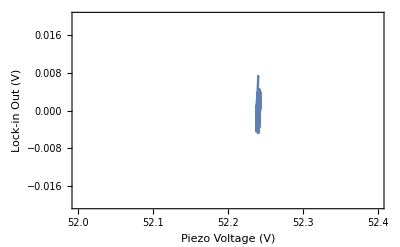

```mathematica
ListLinePlot[{xdat,ydat}ᵀ,PlotRange->{{52,52.4},{-0.02,0.02}},Frame->True,FrameLabel->{"Piezo Voltage (V)","Lock-in Out (V)"}]
```

```mathematica
Close@laser370
```

192.168.32.4:1998

```mathematica
laser@Dispose[]
Clear[laser]
```

```mathematica
laser=NETNew["NationalInstruments.VisaNS.MessageBasedSession","TCPIP::"<>"192.168.32.4"<>"::1998::SOCKET"]
```

«NETObject[NationalInstruments.VisaNS.MessageBasedSession]»

```mathematica
laser@TerminationCharacterEnabled=True
```

True

```mathematica
laser@TerminationCharacter=ToCharacterCode[">"][[1]]
```

62

```mathematica
laser@DefaultBufferSize=2^15
```

32768

```mathematica
laser@ReadString[]
```

```mathematica
laser@Write["(param-ref 'laser1:scope:data)\n"];
```

```mathematica
SigDisp=laser@ReadString[]
```

"eTQwOTIAqYYsO8+p1zp4diM7F2IfOhDWDTuqYt46HJOPOkHGrjrChSY62R+SuUXxc7pEhl44VwcauyWEL7qyY3K7XLOTulaakbvgtRC7sYsmuwizTLvBlRq7hw02u71Slbq7TOq6qBWQuccZYLo34720ODr5NjHagTq4oJQ6tUOuOm4ETzsgRzE7H8riOjBTRjtrSqY66aoWOwZazDl6Vjs7emCoODWSCTs0kES5woUmOtghM7r05mO6sYWfuvmmN7uz0u26MNyiuhuN5LplfP+6tiVnunrfF7uxBrC6YzU4u6RFyLk5TLK69WMyOpTOnblSKX83qnSXOlh2Fbkdf7U6/JKBOjfjvTqRZ0o7VfvnOnF1DzvRfeE6gmWiOlQvqjoaLLw6Y0UsOghMnTrbds04UydeOQX5o7qIZPG6iAGouv3fz7rD5s66FlrTuj32ZrrmWwO7zd2Zulh2lbnzDpi5uKAUOgo0gTo0kEQ6b4sKO6U5ujpMKI86PAxiOhq1GDp4gBA7VftnOoHmsjrwFPs5Btm7OVsia7mjR2k5QF06uhsWwboEBTK3N/eXugqht7roosq6XZXMuj0AVLtobK+6uXhgugKI47nfUIK6Tn/KuHW4lDnjcVq5lbgiOmcHITs5OFg6Xv5AO8zbVDsZNik7X/g5O8cnMzs8Fs86xyPNOpaQbjohOyM7mfdBOf5U0jqwpQc6IUWQuY4K5LqaTv26W0QYu+qMT7uooA27u2ZLuyfPXLvookq7MjE9uw0ChLsLgU+7rUghu6Yb87lTzoG5/t2uuQsCYDkKq6S4HuRDOxKS1zqT2qs7uoQSO0nVlTv+5xs7v6cvO2YdHDt2ohk6PQDUOocDyTnGL1s5/IiUur7RBLvKdsa61FVRu6r1J7sVeBq7IR/9uuP+HLtmhEu6qHr6ugbjKLujXym7Xvb0OacrC7r+8Qg7WHAOOzd8Djv1Y7K5AikAO2cBGjqRcbc6CbsYO2SS+jqgpYA6T32puYNZlLiRXd26XR6pt4asDTn7CSW5YW8BuYNFOjqtq+q6qBWQuXWQ4LqBXda4Aqaqum4UwzkRqNK5jwD3Ofe4TLkEBbI4+4q1OUqtYTpx3L46xVcPO6h6+jrQMJM6OzQWO6+7gjlGgpw4CwJgOTaMAjr6C8a4lE0NOt1K17nxElq4oXE+us5SnLm0bYO6QVuZuYNZFLjgHmE6LX88upl2sbrnpOu65AIDutiiw7nzjyg6pUOnuU7+ubl54Ti6N+M9OFPOAbm/Cnk6fLVCuc+p1znAHDI6Gg51Ort+izrt1Vs6WUxAOvk1GzoAM8k52+HiOgIrITtA8IM6vbVeOibtozn1dwy6gAabuD0KQbpjMVI6i619uo8SMLpcKje7gmWiulBnLrtpWNW6a7FVu3cNr7qFpEG7sJGtuoeE2bqcySq66SkGukYDLbqgmxM6IcoGO8kLsTr/NOo6JXrCOsrtaTrVRd06UGsUOyDcGzq1zqs6gAabOTaMAjqDWZQ3y9fuONe4vrqooA27XRpDu6tuELt4bte6+hWzujsgvLr34AC7hi2eurVJNbuvFN857mYEOn8cFjsQURc5pM6kOhVmYbrLajg6EroLumxIBTvpK6c6eO3GOoBzUbpZ4So6RC2COVMn3jntXrg6FveJOPjKBToFXO21mPliOpmKCzo34z23woWmua8K8rqIjKW6FPvLuMmC1DllGTa5dqyGurH8wrrFMXy4ztELuY8A9zowP+w6Vg2hOqn3yDqnrBu6gV1WOQoqFLpTps052p6BuVHSQ7lSPVk6LZMWOaVXgbqCW7W6gIEkuzpKEbpkG9e5wX3aOh30tzdKLnK5PItRuQTdfbom7aO42CGzOdKPGjppw2q5OTjYOaNjjzrxk+q5Sq3hOkBdujmsQFW5D1O4uZ6fVTZyvne4XnXkOb213rkVeBq6BOfqus8oR7oLFJk6diEJOj6HDzrN5wa6ZgVcutt2zbojB2E6jrGHOve4zDrKGQQ7PCQiO+EcQDmvMIU6WssvOsvXbjnDgwW6WyJrObY3oLkP5gG76aqWurztBrsF6S+7Ju/EuvNn9Lp+Ih27HA4ZuxIlIbrhh9W697jMt+ZDw7lf4Hk60f7xOcAqBTv0CBE7eICQOre2jzoBlPE6e14HuUu/GjqUXQE7l6AGOuVZPjp4ZOo3Rg2auq8K8rprt9y67GDZuuts57oJNqK6YfCRuWut77q2Mzq7wRYru7+V9rqQfUW6RZgXOi0AzTptldM5E/1sOYAGm7ljHfg5k7zkOrASvjkLAuA6iBWCOo6nGjszG8I6SyxROMRZsDrU+A66sehoOKjvfDkeS/O3fp2mOho0CLqPJgo6WtUcu1uje7qdNEA6CFaKOT2JsLngMBo6zlKcOaCbE7r3uMw4tw/sOQNyaDpB2oi5y9duOiMlqLrqnoi6c7xWub3dErlpag66qQE2unS6tbg3Yi26rNMeujfjPbaQ/LS64gbFOgFFAjpZagc70CYmuShEXzpkQwu6np/VuUwqMDr9Xj86sJGtOByTjzrfs0u64a8JOoAGm7gPXaU6aIAJuvVjsrniBkW6+LYrOkYDLbpquf06HHfpObU5wTnptIO6Z27QOFIpfzmh8s64Egn7OjyfKzrWzBi5EajSOfk1mznHLTq6N+O9OXteBzlHbsK6wl1yuqL6mrpP4PK6pDHuuv9gBLv0W+a6s1Fdu9TkNLptFmS6VAf2utzzGzrk3G+6IcagOcvX7jnymRU7IjkCO4D8rTrAJh872LoDO9XYpjrE2sA63HILO9t2TTlNi9g6ZYZsOhb3ibjIqoi6pcwDu8H8yboqLEO7I64Euqp+BLs4WEC7fottu2PWgrvkX0W7PKkYu7Y3oLhHbkK6RC2COeAeYTmFL785e16HOprvGTtkPYQ7WHYVO8ztjTvCCh07Q6ZGO4xOGjsVejs7Wc3QOl+RijrKbFk66xOLORsgLrpSOzi6m9+lus6r+LotGA27wCYfu542BbvS8uO6YW8BuwSEIbsGz866x0EUu8zfurpZuXa6k1mbOgbZuzqSeYM67lKqOmlqDjlodpw6k1mbOmBxIjuetxU7t5D8OpFtUTuhe6s61yX1OvNndDkJmes6DJMIOjwUrjpcIEo6HfS3unh2o7qkT7W6VgM0u9sJF7u7eAS7SWATuzo2t7oV+aq6OOsJu5aQ7rpUKSO70aWVut6/2bqSU3A6emCoOKCbEzuYCxy6Ka1TOkwoDznyEDk7fZthO2nXRDvCCh07xrDrOsTkrTqolqA6NY6jOoAQCDuLrf05SOsQOrP4ALokmAk5/yr9uk5/Sjlsww67v53CujdsGrs4w9W6trIpu8kROLviEDK7YGc1u7GVE7sTfn26et8Xuon/hjilQ6e5HfQ3NwWCgDn7dts6RYQ9OpegBjtlD8k6xzEgO73dkjogP+U6ZnBxOvA8LzqTPXU6/9uNOo00uTod9Dc6xi9buWu/qLoRKeO6s0fwupxKO7rzhbu6+gvGOHl6CbvF0hi7j6ETuwIbrbpA3Kk5E/1sOY/+Vbq8Skk6tsyKuqiCRjrIqog6aGLCOmFJbjoEaPs6jwD3Okdk1TqvCvI6Z4IqOg/SpznXJfU5H0lSOlFRMzqtPjQ6oBqDOWpWNLo38RC7ie3Nuh1/tbocHo25VheOumeCKjrQHLm6NY4juTpKEbrE2kA4V/clOjdiLTqMWAc7EpLXOgfFYTpbyQ46N+O9OXWazTqQaWs6McanOiwKujrzj6g550uPuvySgbrwsbG6f5EYuxEnwrkCL4e6TAL8uTyfq7py0DC67Om1uR11yLl/hys6bhTDOLL6oTrTeZ85P4EIO1V8+LiI7246q1ZQOghWirnJFR46tNq5Os7RCzndSlc67t2nuuxg2bpY48u6eHajupD8tLnylS+7sY8MuY0+JrspSoq6subHutVhAzojmqq4OOEcOmfv4DkEBTI69uKhOaGFGDpTzgE6vTZvOiOuhDptHrA6F7t7OhEnwjlW+cY5sWn5uaaaYrpH9566yCGsulQlvbgKKpS67GpGuV+RCrsG7RW6vkIhu+N7x7rC6O+6OOEcOk/yq7oec6e5y34SuWy9Bzpn7+A5/OHwOtF94To6o+06hS+/OrimGzs1mJA63GDSOjE9S7lOEhQ6GaNfuvC7HrjWTam6tTH1up6zL7sTEUe78qkJu4Qx4LqXoAa6gF/3uQupA7pP/Bg6kWdKOnf5VDp67ws7MxHVOq3HkDouhwg7m0zcOvDFizrJgtQ5P1XuOihE3zqpgKU6EZ7lOsv9gTnBh8e5ZpilubYlZ7p3jJ66J3aAuvc5XTrhqQK7ZpilOa6V77iJ7U26R27CukHaCLnJA2W6F07FuJU5Mzrnmv45xy26uciE9bkBRQK6Jm40uv5KZToQPb06bJd0OiSYCTnGwqQ6+h8guoLcxTk6t8e5cWc8OiFFEDoFXO24FBmTOptogro6Il06xsIkOnO8VrkUjpU6NQ0TutRR6zoyO6q6MroZOg5B/7rKgDO4HQgSuj/eSjmq67q5v7uJuhP97Ll9n8e6E359ukSG3rddnZi67r/gOXpgqLhgcSK5XwYNOnS6tTnNQGO63Ex4OrClhzq3inU7HXVIOmLUDzsvZyA6/V6/uVIpf7iPf+Y5JQMfOpr1oLrChaY5+RdUu7L6IbvuRFe7wKsVu5iCP7vDeZi6uZQGu+7dJ7t61Sq7ZBvXuPmO97qR+hM6yCuZOhb3iTo9BDo7hR9LO6CHOTv7dls7VYZlO1pCUztcsxM7/HpBOx5lVDt9DP65TJVFOlWG5bp9OBi7BfMcuylCPrtz0IK7pU+Hu5Paq7v4MbW7zNmzuySekLtVAW+7UcRwu/OPqLpixjy5oXG+OXgLDjrFP087HltnO0wuljsEcMc7LBSnO9VfkDuoEao76J5kO0jrEDss8nk7wvJcO8eyMDui8K059ObjObPS7bpi5AO763BNuympbbvl7Ie79AqEu4XCiLvE4Jm7F2yMu5kHiLuxc2a7zyjHut1KV7pGA606i9WxOlpUDDvPHto6qnoeOysuCDtXAZM7WzZFO4AOlTvhICY7PvRFO7GFHzsBwAs7hSXSOjZuuzocjyk7Yx14ObF9UzpzvFY5RIbeukaMiboSpjG6N2Ktukjho7qWpMi5nSDmupHo2rqHhNm6TBbWut1A6roIVgq6emAoujsgPLp4BQe7RZiXuq+TTrozG8K60JPcOpJT8Dk+a+k66JhdOrtMajrHwIM6DmMsO548DDvUXz47qKANOy/oMDuPAPc5UqjuOm0W5DlEhl66MD/sueoVLDm1ulG6om8du193KbvQEky7hCtZu9sLirtG79K6y2BLu30yEbr5Dee53N9BujVw3LpJVqa5itfSuWYhgjrhFjk7Ojw+OyVw1TraeO46uBe4OpYR/zqxjww6xFVKO4Q5rDoSL446WTQwOTIAAQBDuwEASLsBwDK7ASBGuwEgKLsBICi7AcAouwHgIbsBwCO7AQAvuwHAN7sBYC67AQBSuwGARbsCQHa7AYBeuwEQi7sBoIK7AXCKuwHQk7sBsJW7AeCcuwFAl7sBwJ67ATCYuwHgnLsB0Ji7AdCYuwGwkLsBMI67AdCJuwJAcbsBAGu7AYBtuwHgU7sBAFy7AWBHuwEgWrsBADS7AQBSuwHAMrsBYEy7AeA/uwEAUrsBwFW7AWBguwIgfbsC4Hu7AqB6uwFwhbsB0Im7AVCHuwHgkrsB8JG7AWCfuwHgkrsBkJy7AcCPuwGglrsBIJS7AVCMuwHgkrsBQIi7AQCHuwGwgbsBAGG7ASBpuwHgWLsBAFe7AcBVuwHAULsBgEW7AYBPuwGgQ7sBAFK7ASBQuwFAZ7sCAHW7AoByuwJgfrsBUIK7AbCGuwHQhLsBYJC7AUCNuwEwibsBIIq7ARCGuwEggLsCoH+7AQBmuwGAaLsBAGa7AWBluwEgZLsB4Em7AcBVuwGASrsBoFK7AYBPuwFAWLsBwFC7AeBduwFAbLsB4F27AWBvuwKAd7sBIIC7AfCCuwEwk7sB8Iy7AbCLuwFQjLsBAJG7AfCMuwFwirsBgI67ATCJuwJgdLsBsIG7AQBhuwHAULsBYEy7AQA+uwEANLsBgDu7AWAzuwGANrsBwBm7AcAyuwFgGrsBgCK7AcAtuwGgQ7sB4E67AYBZuwKgcLsB4Gy7AQCCuwHAirsBEJC7ARCVuwFwo7sBUKW7ATCnuwHgnLsBkJy7AdCduwHAmbsBUJu7AZCDuwGgh7sBAFK7AQBruwGgPrsBIEu7AcA8uwEgN7sBgEW7AcAyuwEAPrsBoD67ASBVuwFAZ7sBgGi7AfCCuwFwhbsB0Im7AcCKuwEglLsBAIy7AfCWuwGgoLsB8KW7ASCUuwHAmbsBkIi7AUCDuwKgf7sBMI67AgB6uwGQg7sCoHW7AYBjuwGAXrsBgGO7AqB1uwJAcbsBcIW7AiB4uwIAdbsCAHq7AsB4uwEgbrsBYIa7AmB+uwEQi7sBUIK7AVCMuwHwgrsB8Ie7AVCCuwFQh7sBcIW7AaCCuwIAf7sC4HG7AeBiuwHgXbsBoGG7AcBLuwGAY7sBIGS7AeBiuwHAWrsBQGK7ASBauwGgZrsBoGG7AeBsuwEgabsCIHi7AkBxuwIAcLsBoGG7AgB6uwGggrsBkIi7AaCCuwGggrsCwHO7AgB/uwHAgLsBgIS7AcCAuwEQgbsCwHO7AsB9uwKgdbsCoHC7ASBpuwHgYrsB4GK7AcBfuwEAYbsBwF+7AaBNuwGgObsBQEm7AeBEuwFgTLsBoFe7AQBSuwGgXLsBwEa7AeBduwHgXbsCYH67AoByuwFghrsB0IS7AdCTuwFQjLsB8Ju7AXCUuwHAmbsBEJW7ARCVuwFAl7sBgI67AZCDuwGQg7sCoHq7AmB0uwLgdrsBAGa7AWBWuwHAZLsBAFe7AcBfuwEAXLsBYGC7AcBfuwLgdrsBoIK7AeCNuwGwi7sB8Iy7AUCNuwFQkbsB4Je7AeCXuwFAprsBcJS7AZCSuwEwhLsB0I67ARCGuwEwk7sB4Ii7AQCRuwLge7sBcIC7AoB3uwGAibsBcIC7AbCBuwFwgLsCoHC7AsB9uwLgdrsCwH27AkBxuwLAc7sCYHm7AqB/uwFgi7sBsIu7AeCDuwEggLsBEIG7AZCIuwGgjLsBcIW7ARCGuwEgbrsBQGe7AUBnuwHgXbsCgHe7AYBtuwLgdrsBQGy7AoByuwIAdbsBAGa7AYBtuwIAf7sBMIS7AcCPuwEQhrsBYIa7AeBsuwKgf7sBsIG7AXCAuwEAh7sBsIG7AmB+uwLgdrsBsIG7AsB4uwKgcLsBYIG7AWBluwLgcbsCoHq7AoB8uwLAeLsCwHi7AuBxuwLAeLsCgHy7AcCKuwEQhrsCwHO7AiB4uwJAdrsBcIC7AdCEuwHAirsCwHi7AgBwuwGAY7sBIFW7AWBHuwFgYLsBoFK7AUBTuwGAVLsBYGC7AcBQuwHgWLsC4HG7AWBvuwEQgbsBAIy7AeCIuwHQjrsBoJa7AWCauwHwkbsBoJu7AZCSuwFglbsBYIu7AeCNuwLAfbsCgHK7AsB4uwJgdLsBAGG7AoB3uwHgbLsBQFO7AUBiuwFgW7sBgGO7AiBzuwGwgbsBMIS7AQCHuwFgi7sBIIq7AdCEuwGwkLsBkJy7ARCfuwFQoLsBoJu7AdCTuwFwirsBMJO7AeCSuwEAlrsBAJG7ARCGuwHwjLsBYIG7AdCEuwHAbrsCYHS7AQCCuwIAcLsBkIO7AXCAuwJgfrsBcIC7AoByuwGQg7sCAHq7AUCSuwEAjLsBEIG7AaCCuwEAh7sBcIC7AbCBuwHwh7sBIIW7AaCCuwIgfbsBIIW7AmB5uwEQi7sBUIy7AVCHuwGwhrsBEIu7AeCNuwGAibsB0I67AZCNuwEAjLsBYJW7AdCEuwHgiLsCYHm7AZCIuwGwgbsB0Im7AcCKuwGQg7sBAIK7AdCEuwIAersBQIi7AgB/uwGAhLsCwHO7ASCFuwFwhbsBMIm7AsB9uwGgh7sBYGq7AiB4uwLAeLsBEIa7AgB/uwIAersCoH+7AeBduwEgabsCYHS7AUBsuwFAbLsCYHm7AaBruwHAbrsBkIO7AfCCuwEQhrsBMI67AaCRuwHwlrsB0Ji7AbCpuwFgmrsBMJ27AfCluwGQl7sBgKK7AbCauwHAmbsBEIu7AUCIuwHQibsC4Hu7AoB3uwJAe7sCwHO7AUBiuwKAd7sBAGG7AWBluwJgdLsBYIG7ARCLuwEAjLsBUJu7AYCOuwEAm7sB8KW7ASCyuwHQu7sBYL27AaC+uwHAsrsBALm7ARCzuwEQs7sBgLG7AUCruwEgnrsBAIy7AaCRuwKgersBoIK7AkBxuwFgb7sBQF27AcBkuwGgZrsBYGW7AcBpuwJAdrsCQHa7AWCBuwHgiLsBwI+7AQCWuwGAmLsBYJq7AWCfuwFwqLsBMKe7AQCvuwEgrbsBIK27AXCeuwEAm7sBAJu7AfCWuwGQnLsBcJS7AZCSuwEQhrsB8IK7AcCAuwHgZ7sCQHa7AYBouwIAersBoFy7AUBsuwEgWrsBAGG7AgB/uwGggrsBEIa7AXCUuwHwlrsBIJm7AWCfuwGAnbsBQKG7AbCpuwHQrLsBkLW7AUCwuwHQtrsBQKa7AbCpuwHQmLsB8Kq7AZChuwGgpbsBsJC7AbCGuwEAgrsBIIC7AXCAuwKgf7sCgHy7AuB2uwEAZrsCoHW7AmB0uwHAgLsCAHq7AUCNuwEQgbsBgJO7ATCTuwGQnLsBQJy7AeCmuwHArbsBsLO7AbC4uwGAu7sBkLW7AaC0uwFAsLsBwLK7AUCwuwGwrrsBcKO7AUCmuwEQmrsBAJu7ARCQuwEQlbsBMI67AQCRuwFgkLsB8Iy7AeCIuwGAhLsBUIe7AVCMuwEglLsBsJq7AcCeuwFgmrsBkKG7ASCZuwGwqbsBAK+7AbCzuwGAsbsBIKi7AXCouwHgsLsBQKa7ASCyuwGQprsBMKK7AZCcuwHQnbsBwJS7AbCQuwEwjrsBMIm7AeCNuwEgj7sBoIy7AeCIuwFAiLsBYIa7AUCIuwGAjrsBQJy7AfCbuwFwnrsBgJi7AWCfuwEglLsBMKK7AaCbuwGgoLsB4Jy7AbCauwEwmLsB4I27AQCMuwFwj7sB0I67AYCOuwEAh7sB8Ie7ATCEuwEggLsBwIW7ASCPuwEAkbsBYJW7AbCfuwGAk7sBwJm7AfCWuwEgnrsB8Ju7AbCauwFAnLsB0JO7AfCWuwFQjLsBUJG7AWCBuwGQjbsBEIa7AYCEuwEAjLsBgIS7AgB6uwHwgrsCoHq7AVCMuwHwkbsBYJW7AVCWuwFAkrsB0KK7AWCVuwGAp7sBMKK7AZCmuwFQm7sBgJ27AcCZuwHQmLsBkJe7AdCYuwGQl7sBoJa7AeCSuwFgkLsBAIy7ARCLuwGAjrsBUIy7AUCSuwGwlbsBsJq7AZCcuwGglrsBIJ67AQCbuwEQqbsBsKS7AQC0uwFQtLsBoLm7AeCruwHAt7sBYLO7ATCxuwFwrbsBIK27AZChuwFwnrsBYJq7AXCZuwFwj7sBcJS7AdCOuwFwmbsBkJK7AUCcuwEwmLsB4KG7AQCquwGws7sBcLy7AYC7uwEQvbsBcLe7ARC4uwGQursBYLO7AeCwuwFAsLsBEKS7AaCluwFAprsBoJu7AWCauwFwmbsBkJy7AXCPuwEwjrsB4I27AVCHuwFwj7sBoJG7AeCSuwEAlrsBoJu7AaCbuwEQkLsBYKS7AfCWuwEQmrsBEJ+7AZCmuwEwnbsBEKS7AWCfuwEQmrsBYJq7AXCeuwEAoLsBYJ+7AeChuwGAmLsBoJG7AeCSuwFQlrsBQI27ATCYuwFAkrsBAJa7ASCPuwHQjrsBkJK7AYCJuwGQl7sBAIy7AUCNuwEAkbsBkIi7AUCSuwEAgrsBEJW7AdCJuwGgm7sBAJG7AZCXuwHgkrsB0Ji7AdCduwFQm7sBsKS7AcCjuwGwn7sBcKi7AaCguwEgo7sBYKS7AWCfuwEAoLsB4Ka7AQCbuwHgl7sBEIG7AVCRuwEwhLsBYIu7AQCRuwFwj7sBEIu7AeCIuwEQlbsBAIy7AQCluwFAprsBgLG7AYCxuwHgursBYLO7AWC9uwGgw7sB4Mm7AYC7uwGQybsBILy7AeC1uwFQtLsBEKS7AUCcuwFQlrsBoIy7AYCEuwIAf7sBIIC7AUBsuwGgXLsBkIO7AqB1uwFAjbsBcJS7AQCbuwHQorsB4LC7AeC6uwFgzLsBUNe7AYDjuwEQ5bsBcOm7AlDwuwFQ5rsBEOC7AfDcuwHA2rsBkMS7ATC7uwFAq7sB8Ja7AQCRuwEQi7sCIHi7AsB4uwLAfbsBwFq7ASBQuwGAT7sB4Ge7AWBluwFQgrsBQIi7AWCVuwEAoLsBIK27AZC1uwEAvrsBIMu7ARDRuwGA2bsB8Ny7AdDUuwGg0rsBwMG7AfC+uwGgtLsBsLO7AfCquwGAp7sBEJC7AVCRuwJgfrsBgIS7AoB3uwIAdbsBYG+7AUBsuwGga7sBwFC7AqBwuwEAZrsCAHC7AXCFuwGwhrsBwIW7AVCMuwHQjrsBwIq7AWCVuwGAmLsBQJy7AQCguwGwpLsBYJ+7AaCguwEgo7sBUK+7ASCtuwHQrLsBULS7AWCfuwFQpbsBAJu7AXCeuwGgm7sBgJi7AQCMuwHQibsCwH27AsB9uwGga7sBcIC7AQBruwJgebsBwIW7ATCEuwFwgLsBgIm7AVCWuwEQn7sBMKe7AZCwuwHAvLsBILK7ASDBuwFQtLsB0La7AbC4uwFQw7sB4Lq7AcC8uwHAsrsB0KK7AUCcuwEQn7sBwJm7AdCYuwEAkbsBkJe7AQCCuwEgirsB4Ii7eDQwOTIAXO1QQl/tUEK27VBCL+1QQsjtUELZ7VBCyu1QQvrtUELw7VBC0u1QQqDtUELK7VBCTe1QQmHtUEKr7FBCB+1QQh/sUEJO7FBCP+xQQs/rUEK761BCwutQQqzrUEKJ61BCuOtQQo7rUEKk61BCoutQQvfrUEL561BCROxQQoPsUELQ7FBCxOxQQhTtUEL47FBCZu1QQv3sUEK57VBCPu1QQrHtUEJc7VBCZO1QQhvtUEIl7VBCB+1QQpTsUEKS7FBCfuxQQknsUEIh7FBCIexQQuXrUELv61BCf+tQQujrUEKE61BCxetQQuXrUEK961BCAexQQt7rUEIf7FBCK+xQQnvsUELT7FBCy+xQQh7tUEJB7VBCLe1QQjntUEJw7VBCQ+1QQnXtUEI57VBCJe1QQtDsUEKZ7FBCt+xQQoXsUEJW7FBCU+xQQmLsUELj61BCH+xQQh/sUEIa7FBCNexQQnbsUEJv7FBC6exQQqPsUELd7FBC3+xQQvPsUEJX7VBCDO1QQlDtUEJD7VBCKO1QQgftUEI37VBC7uxQQrXsUEIl7VBCuuxQQorsUEKF7FBCZexQQuXrUEIk7FBCQuxQQlPsUELv61BCCOxQQivsUEL061BCJOxQQp7sUEJ27FBC8+xQQjTtUEJh7VBCp+1QQrntUEKC7VBCjO1QQsjtUEIB7lBCrO1QQhruUEL87VBCxe1QQk3tUEIv7VBCHu1QQrrsUELO7FBCiuxQQivsUEIf7FBC2+tQQmbrUEJc61BCaOtQQonrUEKL61BCkOtQQp3rUEKJ61BCR+xQQkfsUEIP7VBC/exQQn/tUEI37VBCie1QQqftUEJk7VBCu+1QQmvtUEJ/7VBC+OxQQqjsUELB7FBCWOxQQibsUEIz7FBCR+xQQujrUEIh7FBCyutQQnfrUEJc61BCz+tQQrjrUEIf7FBCVuxQQpzsUEIV7FBCZexQQljsUEKF7FBC2OxQQgrtUELV7FBClOxQQsHsUEI47FBCl+xQQo/sUEKZ7FBCmexQQqPsUEI/7FBCo+xQQiTsUEJR7FBCH+xQQk7sUEJC7FBCb+xQQjPsUEJ07FBCbOxQQojsUEK67FBC0+xQQunsUELa7FBCPO1QQtjsUELs7FBC3+xQQg/tUEIU7VBCGe1QQtXsUEL77FBC0+xQQr/sUEKt7FBCvOxQQojsUEL77FBCjexQQmzsUEIh7FBCbOxQQmLsUEKw7FBCo+xQQnbsUEJJ7FBCfuxQQnnsUEKo7FBCgOxQQsTsUELB7FBCxOxQQgrtUELY7FBCAu1QQuTsUEIF7VBCLe1QQqDtUEJD7VBCZO1QQkvtUEIF7VBCHu1QQjLtUEJc7VBCB+1QQgXtUEJ27FBCv+xQQjPsUEJb7FBC4+tQQgPsUEJ661BC3utQQpXrUELH61BCvetQQsfrUEIX7FBCXexQQkfsUEKS7FBCkuxQQqHsUELn7FBCCu1QQt3sUEJD7VBCAu1QQvHsUELz7FBC5OxQQqPsUEJO7FBC9OtQQgvsUEL+61BCEOxQQuDrUEKL61BCwutQQkrrUELg61BC1utQQnvsUEID7FBCH+xQQurrUEIf7FBC2+tQQn7sUEJn7FBCauxQQj3sUEJs7FBCduxQQoPsUEKh7FBCauxQQqHsUEKK7FBCvOxQQqPsUEJ27FBCgOxQQibsUEL+61BCROxQQoXsUEJb7FBCPexQQgjsUEJW7FBCTuxQQrfsUELL7FBCy+xQQiDtUEKj7FBCtexQQqPsUEKy7FBCpuxQQo/sUELn7FBCy+xQQnHsUEJg7FBCAexQQjjsUEJv7FBCzuxQQoDsUEJ77FBCcexQQjDsUEJY7FBCg+xQQpnsUEJv7FBCoexQQr/sUEJE7FBC5+xQQtXsUEKX7FBChexQQs7sUEKh7FBCmexQQp7sUEKX7FBCDexQQlHsUEJ07FBCoexQQp7sUEJ07FBCXexQQj/sUEKZ7FBCnOxQQtXsUEIP7VBCYe1QQhvtUEIq7VBCS+1QQjLtUELi7FBCTe1QQh7tUEKe7FBCq+xQQnnsUEL561BCOuxQQvfrUEKu61BCx+tQQu/rUEK461BC2+tQQrvrUEIk7FBC9OtQQpfsUEK37FBCnOxQQpLsUELu7FBCo+xQQrLsUEI07VBC7OxQQvbsUEIR7VBCsOxQQmfsUEJb7FBCEOxQQibsUEIS7FBCdOxQQgHsUEKT61BCYetQQpXrUELC61BC4+tQQhDsUELq61BC6OtQQtnrUELb61BCPexQQjXsUEJg7FBCb+xQQsHsUEKU7FBCbOxQQrDsUEJM7FBCl+xQQoPsUEJg7FBCt+xQQkzsUEJ77FBC8utQQgPsUEJ27FBCbOxQQjXsUEJl7FBCdOxQQiTsUEJO7FBCR+xQQm/sUEJT7FBCkuxQQiTsUEI97FBCSexQQjjsUEIk7FBCEOxQQknsUEL561BCA+xQQgbsUELe61BCTuxQQjXsUEKA7FBCH+xQQojsUEIc7FBCKexQQljsUEJl7FBCTuxQQpfsUEIm7FBCdOxQQl3sUEK17FBCP+xQQk7sUEIw7FBCiuxQQiTsUEK37FBCl+xQQoXsUEIz7FBClOxQQpTsUEKI7FBCAu1QQrfsUEKP7FBCzuxQQtDsUEKe7FBC5OxQQsTsUEJH7FBCfuxQQlHsUELy61BC/OtQQqnrUEKi61BCO+tQQpDrUEKO61BCUutQQuDrUEJo61BCrutQQqzrUEJi7FBCW+xQQj3sUEKr7FBCoexQQpfsUEK/7FBC+OxQQmfsUEL97FBCzuxQQp7sUEJ57FBCKexQQiHsUEKL61BCDexQQo7rUEJI61BC1+pQQqDqUEJ96lBCeOpQQv3qUELV6lBCy+pQQu7qUELX6lBCB+tQQpDrUEIh7FBC/OtQQpfsUEJl7FBCuuxQQsbsUEIq7VBC6exQQvHsUELV7FBC3exQQoPsUEKo7FBCiOxQQj3sUELl61BC0etQQrjrUEKs61BCbetQQjHrUEIv61BCDutQQhjrUEIs61BCjutQQqzrUEKQ61BC1utQQq7rUEL361BC7+tQQkTsUEJq7FBCgOxQQs7sUEK17FBCwexQQpnsUEIW7VBCsuxQQgDtUEL97FBChexQQkLsUEIz7FBC+etQQtnrUELC61BCgetQQpXrUEJ361BCVOtQQjTrUELz6lBCAutQQsvqUEJS61BCOetQQqLrUEIs61BCf+tQQnXrUEL+61BCTOxQQnTsUEJ+7FBCmexQQm/sUEJ57FBCiuxQQuTsUEKZ7FBCyexQQnbsUEJn7FBC+etQQnTsUELj61BC7+tQQovrUEKi61BCSOtQQu7qUELG6lBCt+pQQqXqUEIE61BCyOpQQunqUELp6lBCAutQQvrqUEJe61BCUutQQnfrUEKp61BCA+xQQrvrUEIQ7FBCz+tQQgPsUELg61BCHOxQQlHsUEJH7FBCHOxQQhXsUEKs61BCietQQpDrUEJ/61BCpOtQQk3rUEIH61BCyOpQQvXqUEIJ61BCIutQQuHqUEJF61BC4epQQk3rUEJc61BCqetQQnXrUELg61BC8utQQvLrUEIz7FBCEOxQQu/rUEL+61BCOuxQQiHsUEI17FBCIexQQgjsUEKE61BCnetQQnzrUELA61BCi+tQQuDrUEKE61BCn+tQQnzrUEKz61BCu+tQQrjrUEIQ7FBCIexQQg3sUEID7FBCKexQQhDsUEJO7FBCW+xQQkfsUEJb7FBC9OtQQgHsUELW61BChOtQQtnrUEKu61BCzOtQQpPrUEKQ61BCjutQQprrUELj61BCwOtQQibsUEL361BCjexQQgPsUEJM7FBCXexQQgjsUEJM7FBCkuxQQmrsUEJ57FBCFexQQvLrUELR61BC0etQQvLrUEJe61BC1OtQQizrUEJS61BCRetQQqfrUEJm61BCn+tQQp3rUEKL61BCs+tQQrPrUEKz61BC6utQQuDrUEIm7FBCJOxQQhLsUEL561BC3utQQrbrUEKu61BCi+tQQszrUEKu61BCjutQQhvrUEJo61BC/epQQtrqUEK06lBCAutQQsPqUEL96lBC3+pQQirrUEIO61BCcutQQp3rUEKk61BCn+tQQgPsUELU61BCAexQQs/rUELR61BCgetQQq7rUEJZ61BCEetQQsvqUEJs6lBCpepQQn3qUELI6lBCo+pQQo/qUELk6lBCDutQQgLrUEJh61BCcOtQQk/rUEJy61BCp+tQQpjrUEKE61BCA+xQQu/rUEL361BCR+xQQgjsUEIQ7FBC7+tQQsfrUEK261BCjutQQsfrUEJ661BCyutQQovrUEKL61BCE+tQQnrrUEJj61BCietQQrHrUEK761BCletQQmbrUEJ861BCVOtQQqTrUEL061BCz+tQQszrUEIa7FBCvetQQvLrUEK961BCFexQQgjsUELP61BCJOxQQsXrUEIh7FBC+etQQujrUEIf7FBC7+tQQnnsUELb61BCJOxQQqTrUEIB7FBCxetQQuXrUEJ861BCk+tQQobrUEJX61BCYetQQn/rUEIx61BCY+tQQonrUEIs61BChutQQnfrUEIv61BCqetQQrHrUEJi7FBC9+tQQjrsUEIm7FBCAexQQgHsUEI47FBCTuxQQtHrUEIf7FBCVOtQQkXrUELc6lBC+upQQpHqUELS6lBCqOpQQmTqUEIe6lBClOpQQiPqUEJk6lBCrepQQrTqUEJD61BCn+tQQqnrUEIS7FBCROxQQmfsUEKc7FBCv+xQQg/tUEJl7FBCkuxQQhrsUELH61BCa+tQQlLrUELz6lBCmepQQiPqUEKw6VBCg+lQQkLpUEIY6VBC/OhQQjvpUEJb6VBCs+lQQo3pUEJJ6lBCqOpQQifrUEKs61BC8utQQhLsUEKD7FBCiuxQQp7sUEIU7VBCPu1QQiPtUELY7FBC5OxQQm/sUEIm7FBC1utQQmPrUEI061BCvOpQQoDqUEJB6lBC9ulQQpLpUEKa6VBCvelQQtPpUEJa6lBClOpQQsPqUELp6lBC9epQQhjrUEL561BCEOxQQoPsUEJn7FBCnuxQQqvsUEKr7FBCwexQQtPsUEI87VBCpuxQQtXsUEKh7FBCVuxQQkfsUEIp7FBCIexQQgvsUEJM7FBCzOtQQqLrUEKE61BCfOtQQkrrUEJo61BCeutQQmjrUELp6lBC+upQQhjrUEK+6lBCdetQQlfrUEKs61BCcutQQpPrUEK261BCIexQQknsUEKK7FBChexQQs7sUEJd7FBC2uxQQo/sUEI17FBCYOxQQn7sUEI47FBCmOtQQoHrUEJI61BCvupQQmLqUELc6lBChepQQsjqUELp6lBCnupQQnPqUELD6lBCeOpQQgLrUEJt61BCmutQQqLrUEKz61BCvetQQvTrUEKn61BCcexQQjDsUEI97FBC"
>

```mathematica
ba=BaseDecode[SigDisp];
```

```mathematica
dat=Partition[Normal@ba,4098];
```

```mathematica
ydat=ImportString[FromCharacterCode[dat[[1,7;;-1]]],"Real32"];
xdat=ImportString[FromCharacterCode[dat[[3,7;;-1]]],"Real32"];
```

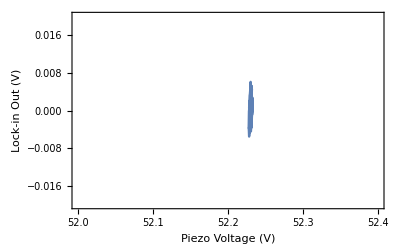

```mathematica
ListLinePlot[{xdat,ydat}ᵀ,PlotRange->{{52,52.4},{-0.02,0.02}},Frame->True,FrameLabel->{"Piezo Voltage (V)","Lock-in Out (V)"}]
```